```mathematica
$Assumptions=And[y[1]∈Reals,y[2]∈Reals,y[3]∈Reals,η∈Reals,ζ∈Reals,0<θ<π/2,0<ϕ1<2π,0<ϕ2<2π];
```

À HOMOGENEISER
notamment : eta = eta33114

## Old pot

```mathematica
√3//N
```

1.73205

```mathematica
(*[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_]:*)
```

```mathematica
Vold=0.001953125*(256*x1^4*Exp[8*x7+1.15470053837925*x9]-724.077343935025*x1^3*x10*x2*Exp[8*x7+x8+1.15470053837925*x9]-256*x1^3*x3*(-x10*x12+2.82842712474619*x11)*Exp[8*x7+0.5*x8+2.02072594216369*x9]-2896.3093757401*x1^2*x12*x4*x5*Exp[6*x7+0.5*x8+1.44337567297406*x9]+2048*x1^2*x4^2*Exp[6*x7+x8+0.577350269189626*x9]+1024*x1^2*x5^2*(x12^2+2)*Exp[6*x7+2.3094010767585*x9]+512*x1^2*Exp[10*x7+x8+1.73205080756888*x9]-362.038671967512*x1*x10*x2^3*(x10^2+2)*Exp[8*x7+3*x8+1.15470053837925*x9]-2896.3093757401*x1*x10*x2*x4^2*Exp[6*x7+2*x8+0.577350269189626*x9]-724.077343935025*x1*x10*x2*Exp[10*x7+2*x8+1.73205080756888*x9]-16*x1*x3^3*(-24*x10*x11^2*x12-x10*x12*(x12^2*(x10^2+8)+16)+22.6274169979695*x11^3+2.82842712474619*x11*(x12^2*(3*x10^2+8)+16))*Exp[8*x7+1.5*x8+3.75277674973257*x9]-512*x1*x3*x5^2*(x12^2+2)*(-x10*x12+2.82842712474619*x11)*Exp[6*x7+0.5*x8+3.17542648054294*x9]-256*x1*x3*(-x10*x12+2.82842712474619*x11)*Exp[10*x7+1.5*x8+2.59807621135332*x9]+1024*x1*x4*(x10*x12*(x1*x6+4*x2*x5+x3*x4)+2.82842712474619*x11*(x1*x6-x3*x4))*Exp[6*x7+1.5*x8+1.44337567297406*x9]-512*x1*x5*(1.4142135623731*x10*(4*x1*x6+x12^2*(x1*x6+2*x2*x5+2*x3*x4)+4*x2*x5)+x11*x12*(4*x1*x6-8*x3*x4))*Exp[6*x7+x8+2.3094010767585*x9]-1448.15468787005*x12*x4*x5*(x12^2+2)*(4*x5^2+1)*Exp[4.0*x7+0.5*x8+2.59807621135332*x9]-2896.3093757401*x12*x4*x5*(4*x4^2+1)*Exp[4.0*x7+1.5*x8+0.866025403784439*x9]-724.077343935025*x12*(4*x2^2*x4*x5*(4*x5^2+1)-x2*(4*x1*x4*x6*(8*x5^2+1)+4*x3*x4^2*(8*x5^2+1)+4*x3*x5^2+x3)+4*x5*(4*x1^2*x4*x6^2+x1*x3*x6*(8*x4^2+1)+x3^2*(4*x4^3+x4)))*Exp[2*x7+1.5*x8+2.02072594216369*x9]+64*x2^4*(x10^2+2)^2*Exp[8*x7+4*x8+1.15470053837925*x9]-64*x2^3*x3*(x10^2+2)*(1.4142135623731*x10^2*x12-4*x10*x11+5.65685424949238*x12)*Exp[8*x7+3.5*x8+2.02072594216369*x9]+1024*x2^2*x4^2*(x10^2+2)*Exp[6*x7+3*x8+0.577350269189626*x9]+512*x2^2*x4*x6*(x10^2+2)*(x10*x12+2.82842712474619*x11)*Exp[6*x7+3.5*x8+1.44337567297406*x9]+64*x2^2*x6^2*(x10^2+2)*(x10^2*(x12^2+8)+5.65685424949238*x10*x11*x12+8*x11^2+16)*Exp[6*x7+4*x8+2.3094010767585*x9]+256*x2^2*(x10^2+2)*Exp[10*x7+3*x8+1.73205080756888*x9]-8*x2*x3^3*(1.4142135623731*x10^4*x12^3-12*x10^3*x11*x12^2+5.65685424949238*x10^2*x12*(6*x11^2+3*x12^2+4)-32*x10*x11*(x11^2+2*x12^2+2)+45.254833995939*x12*(x11^2+x12^2+2))*Exp[8*x7+2.5*x8+3.75277674973257*x9]-32*x2*x3*x6^2*(1.4142135623731*x10^4*x12*(x12^2+8)+4*x10^3*x11*(x12^2-8)+5.65685424949238*x10^2*x12*(-2*x11^2+x12^2+12)-32*x10*x11*(x11^2-x12^2+2)+x12*(45.254833995939*x11^2+90.5096679918781))*Exp[6*x7+3.5*x8+3.17542648054294*x9]-128*x2*x3*(1.4142135623731*x10^2*x12-4*x10*x11+5.65685424949238*x12)*Exp[10*x7+2.5*x8+2.59807621135332*x9]-512*x2*x4*(1.4142135623731*x10^2*x12*(2*x1*x6+2*x2*x5+x3*x4)+x10*x11*(8*x1*x6-4*x3*x4)+5.65685424949238*x12*(x2*x5+x3*x4))*Exp[6*x7+2.5*x8+1.44337567297406*x9]-128*x2*x6*(1.4142135623731*x10^3*(8*x1*x6+x12^2*(x1*x6+2*x2*x5+2*x3*x4)+8*x2*x5)+8*x10^2*x11*x12*(x1*x6+x2*x5)+5.65685424949238*x10*(4*x1*x6+x11^2*(2*x1*x6-4*x3*x4)+x12^2*x2*x5+2*x12^2*x3*x4+4*x2*x5)+16*x11*x12*(x2*x5+2*x3*x4))*Exp[6*x7+3*x8+2.3094010767585*x9]+x3^4*(-90.5096679918781*x10*x11^3*x12-11.3137084989848*x10*x11*x12*(x12^2*(x10^2+8)+16)+64*x11^4+16*x11^2*(x12^2*(3*x10^2+8)+16)+(x12^2*(x10^2+8)+16)^2)*Exp[8*x7+2*x8+4.61880215351701*x9]+64*x3^2*x5^2*(x12^2+2)*(-5.65685424949238*x10*x11*x12+8*x11^2+x12^2*(x10^2+8)+16)*Exp[6*x7+x8+4.04145188432738*x9]-32*x3^2*x5*x6*(1.4142135623731*x10^3*x12^2*(x12^2+4)-4*x10^2*x11*x12*(x12^2+8)+11.3137084989848*x10*(-x11^2*(x12^2-4)+x12^4+6*x12^2+8)+32*x11*x12*(x11^2+x12^2+2))*Exp[6*x7+2*x8+4.04145188432738*x9]+8*x3^2*x6^2*(x10^4*x12^2*(x12^2+8)-45.254833995939*x10^3*x11*x12+8*x10^2*(-2*x11^2*(x12^2-4)+x12^4+12*x12^2+16)+45.254833995939*x10*x11*x12^3+(64*x11^2+128)*(x11^2+x12^2+2))*Exp[6*x7+3*x8+4.04145188432738*x9]+32*x3^2*(-5.65685424949238*x10*x11*x12+8*x11^2+x12^2*(x10^2+8)+16)*Exp[10*x7+2*x8+3.46410161513775*x9]-128*x3*x5*(-8*x10*x11*x12^2*(x2*x5+x3*x4)-16*x10*x11*(2*x1*x6+x2*x5)+1.4142135623731*x12^3*(2*x1*x10^2*x6+x2*x5*(2*x10^2+8)+x3*x4*(x10^2+8))+5.65685424949238*x12*(2*x1*x6*(x10^2-2*x11^2)+x2*x5*(x10^2+4)+x3*x4*(2*x11^2+4)))*Exp[6*x7+1.5*x8+3.17542648054294*x9]+64*x3*x6*(-8*x10*x11^2*x12*(x1*x6+4*x2*x5+x3*x4)+x10*x12*(x1*x6*(x10^2*(x12^2+8)+16)+x2*x5*(4*x10^2+16)*(x12^2+4)+x3*x4*(x12^2*(x10^2+8)+16))+22.6274169979695*x11^3*(-x1*x6+x3*x4)-2.82842712474619*x11*(16*x1*x6+x10^2*(-x1*x6*(x12^2-8)+16*x2*x5)-16*x12^2*x2*x5+x3*x4*(x12^2*(x10^2-8)-16)))*Exp[6*x7+2.5*x8+3.17542648054294*x9]+1024*x4*x6*(4*x4^2+1)*(x10*x12+2.82842712474619*x11)*Exp[4.0*x7+2.5*x8+0.866025403784439*x9]+64*x4*x6*(4*x6^2+1)*(24*x10*x11^2*x12+x10*x12*(x10^2*(x12^2+8)+16)+22.6274169979695*x11^3+2.82842712474619*x11*(x10^2*(3*x12^2+8)+16))*Exp[4*x7+3.5*x8+2.59807621135332*x9]-256*x5*x6*(x12^2+2)*(4*x5^2+1)*(1.4142135623731*x10*(x12^2+4)+4*x11*x12)*Exp[4*x7+x8+3.46410161513775*x9]-32*x5*x6*(4*x6^2+1)*(1.4142135623731*x10^3*(x12^4+12*x12^2+32)+4*x10^2*x11*x12*(3*x12^2+16)+11.3137084989848*x10*(x11^2*(3*x12^2+4)+2*x12^2+8)+32*x11*x12*(x11^2+2))*Exp[4*x7+3*x8+3.46410161513775*x9]+64*(x12^2+2)^2*(4*x5^2+1)^2*Exp[4*x7+3.46410161513775*x9]+256*(x12^2+2)*(4*x2*x5^2+x2-4*x5*(x1*x6+x3*x4))^2*Exp[2*x7+x8+2.88675134594813*x9]+256*(4*x4^2+1)^2*Exp[4*x7+2*x8]+(4*x6^2+1)^2*(x10^4*(x12^2+8)^2+11.3137084989848*x10^3*x11*x12*(x12^2+8)+16*x10^2*(x11^2*(3*x12^2+8)+2*x12^2+16)+90.5096679918781*x10*x11*x12*(x11^2+2)+64*(x11^2+2)^2)*Exp[4*x7+4*x8+3.46410161513775*x9]+256*(x10*x12+2.82842712474619*x11)*(4*x1^2*x4*x6*(4*x6^2+1)+x1*(-4*x2*x4*x5*(8*x6^2+1)+4*x3*x4^2*(8*x6^2+1)+4*x3*x6^2+x3)+x6*(16*x2^2*x4*x5^2-4*x2*x3*x5*(8*x4^2+1)+4*x3^2*(4*x4^3+x4)))*Exp[2*x7+2.5*x8+2.02072594216369*x9]-128*(1.4142135623731*x10*(x12^2+4)+4*x11*x12)*(4*x1^2*x5*x6*(4*x6^2+1)-x1*(4*x2*x5^2*(8*x6^2+1)+4*x2*x6^2+x2-4*x3*x4*x5*(8*x6^2+1))+x6*(4*x2^2*(4*x5^3+x5)-4*x2*x3*x4*(8*x5^2+1)+16*x3^2*x4^2*x5))*Exp[2*x7+2*x8+2.88675134594813*x9]-32*(x1*x2*x3^2*(4.24264068711929*x10^3*x12^2-24*x10^2*x11*x12+11.3137084989848*x10*(3*x11^2+2*x12^2+2)-32*x11*x12)+x5*x6*(22.6274169979695*x10*(x12^2+4)+64*x11*x12))*Exp[8*x7+2*x8+2.88675134594813*x9]-128*(x1*x2^2*x3*(-x10*x12*(3*x10^2+10)+x11*(8.48528137423857*x10^2+5.65685424949238))-x4*x6*(8*x10*x12+22.6274169979695*x11))*Exp[8*x7+2.5*x8+2.02072594216369*x9]-128*(x1^2*x2*x3*(4.24264068711929*x10^2*x12-12*x10*x11+5.65685424949238*x12)+22.6274169979695*x12*x4*x5)*Exp[8*x7+1.5*x8+2.02072594216369*x9]+256*(x1^2*x2^2*(3*x10^2+2)+8*x4^2-2)*Exp[8*x7+2*x8+1.15470053837925*x9]+32*(4*x1*x6^2+x1-4*x2*x5*x6+4*x3*x4*x6)^2*(x10^2*(x12^2+8)+5.65685424949238*x10*x11*x12+8*x11^2+16)*Exp[2*x7+3*x8+2.88675134594813*x9]+16*(x10^2*(x12^4*(x5^2*(48*x6^2+4)+4*x6^2+1)+2*x12^2*(x1^2*x3^2*(4*x6^2-1)+8*x1*x3^3*x4*x6-4*x1*x3*x5*(2*x2*x3*x6+1)+x2^2*x3^2*(4*x5^2-1)-4*x2*x3*(2*x3^2*x4*x5+x6)+4*x3^4*x4^2-x3^4+208*x5^2*x6^2+12*x5^2+12*x6^2+3)+16*x5^2*(48*x6^2+4)+64*x6^2+16)+5.65685424949238*x10*x11*x12*(2*x1^2*x3^2*(1-4*x6^2)+8*x1*x3*(2*x2*x3*x5*x6-2*x3^2*x4*x6+x5)+x12^2*(x5^2*(48*x6^2+4)+4*x6^2+1)+2*x2^2*x3^2*(1-4*x5^2)+8*x2*x3*(2*x3^2*x4*x5+x6)-8*x3^4*x4^2+2*x3^4+160*x5^2*x6^2+24*x5^2+24*x6^2+6)+8*x11^2*(2*x1^2*x3^2*(4*x6^2-1)+16*x1*x3^3*x4*x6-8*x1*x3*x5*(2*x2*x3*x6+1)+x12^2*(x5^2*(48*x6^2+4)+4*x6^2+1)+2*x2^2*x3^2*(4*x5^2-1)-8*x2*x3*(2*x3^2*x4*x5+x6)+8*x3^4*x4^2-2*x3^4+32*x5^2*x6^2-8*x5^2-8*x6^2-2)+8*(2*x12^2+4)*(x1^2*x3^2*(4*x6^2-1)+8*x1*x3^3*x4*x6-4*x1*x3*x5*(2*x2*x3*x6+1)+x2^2*x3^2*(4*x5^2-1)-4*x2*x3*(2*x3^2*x4*x5+x6)+4*x3^4*x4^2-x3^4+16*x5^2*x6^2-4*x5^2-4*x6^2-1))*Exp[4*x7+2*x8+3.46410161513775*x9]+512*(4*x1*x4*x6-4*x2*x4*x5+4*x3*x4^2+x3)^2*Exp[2*x7+2*x8+1.15470053837925*x9]+256*(x1^2*(4*x6^2+1)+8*x1*x6*(-x2*x5+x3*x4)+x2^2*(4*x5^2+1)-8*x2*x3*x4*x5+x3^2*(4*x4^2+1))^2*Exp[2*x8+2.3094010767585*x9]+128*(x1^2*(x6^2*(x10^2*(x12^2+8)+5.65685424949238*x10*x11*x12+8*x11^2+32)-8)-4*x1*x6*(-x2*x5*(2*x10^2*(x12^2+4)+5.65685424949238*x10*x11*x12-8)+x3*x4*(-x10^2*x12^2+8*x11^2-8))+4*x2^2*(x5^2*(x10^2*(x12^2+2)+2*x12^2+8)-2)-x2*x3*x4*x5*(-8*x10^2*x12^2+22.6274169979695*x10*x11*x12-32*x12^2+32)+x3^2*(x4^2*(-5.65685424949238*x10*x11*x12+8*x11^2+x12^2*(x10^2+8)+32)-8))*Exp[6*x7+2*x8+2.3094010767585*x9]-512*(1.4142135623731*x1^3*x10*x2*(4*x6^2-1)-2.82842712474619*x1^2*x10*(4*x2^2*x5*x6-4*x2*x3*x4*x6+x4)+1.4142135623731*x1*x10*(x2^3*(4*x5^2-1)-8*x2^2*x3*x4*x5+x2*x3^2*(4*x4^2-1)+2*x3*x6)+1.4142135623731*x10*(2*x2^2*x4+2*x2*x3*x5+x5*x6*(12*x12^2*x4^2+x12^2+16*x4^2-4))+4*x11*x12*x5*x6*(12*x4^2+1))*Exp[4*x7+2*x8+1.73205080756888*x9]-256*(x1^3*x3*(4*x6^2-1)*(-x10*x12+2.82842712474619*x11)-2*x1^2*(-x10*x12+2.82842712474619*x11)*(4*x2*x3*x5*x6-4*x3^2*x4*x6+x5)+x1*(-x10*x12+2.82842712474619*x11)*(x2^2*x3*(4*x5^2-1)-2*x2*(4*x3^2*x4*x5+x6)+x3^3*(4*x4^2-1))-2*x10*x12*(x2*x3*x4+x3^2*x5+x4*x6*(12*x12^2*x5^2+x12^2+40*x5^2+6))+5.65685424949238*x11*(x2*x3*x4+x3^2*x5-x4*x6*(12*x12^2*x5^2+x12^2+8*x5^2-2)))*Exp[4*x7+1.5*x8+2.59807621135332*x9]+32*(-16.9705627484771*x1^2*x10*x11*x12*x3^2+8*x1^2*x3^2*(3*x11^2+2)+x12^2*(x1^2*x3^2*(3*x10^2+8)+32*x5^2-8)+64*x5^2-16)*Exp[8*x7+x8+2.88675134594813*x9]-128*(x1^2*x2*x3*(4*x6^2-1)*(1.4142135623731*x10^2*x12-4*x10*x11+5.65685424949238*x12)-2*x1*(1.4142135623731*x10^2*x12-4*x10*x11+5.65685424949238*x12)*(-4*x2*x3^2*x4*x6+x2*x5+x3*(4*x2^2*x5*x6+x4))+1.4142135623731*x10^2*x12*(x12^2*x4*x5*(12*x6^2+1)+x2^3*x3*(4*x5^2-1)-2*x2^2*(4*x3^2*x4*x5+x6)+x2*x3^3*(4*x4^2-1)+2*x6*(x3^2+32*x4*x5*x6))+4*x10*x11*(x2^3*(-4*x3*x5^2+x3)+2*x2^2*(4*x3^2*x4*x5+x6)+x2*x3^3*(1-4*x4^2)-2*x3^2*x6+2*x4*x5*(12*x12^2*x6^2+x12^2+16*x6^2+4))+5.65685424949238*x12*(x2^3*x3*(4*x5^2-1)-2*x2^2*(4*x3^2*x4*x5+x6)+x2*x3^3*(4*x4^2-1)+2*x3^2*x6+2*x4*x5*(x11^2*(12*x6^2+1)+8*x6^2-2)))*Exp[4*x7+2.5*x8+2.59807621135332*x9]+16*(3*x10^4*x12^2*x2^2*x3^2-16.9705627484771*x10^3*x11*x12*x2^2*x3^2+2*x10^2*(x12^2*(13*x2^2*x3^2+4*x6^2-1)+x2^2*x3^2*(12*x11^2+8)+32*x6^2-8)-11.3137084989848*x10*x11*x12*(5*x2^2*x3^2-4*x6^2+1)+16*x11^2*(x2^2*x3^2+4*x6^2-1)+16*x2^2*x3^2*(3*x12^2+2)+128*x6^2-32)*Exp[8*x7+3*x8+2.88675134594813*x9]+256*(x1^4*(8*x6^2-2)+16*x1^3*x6*(-x2*x5+x3*x4)+2*x1^2*(x2^2*(4*x5^2-1)-8*x2*x3*x4*x5+x3^2*(4*x4^2-1))+8*x1*(x2*x4+x3*x5)+x12^2*(x4^2*(48*x5^2+4)+4*x5^2+1)+32*x4^2*x5^2-8*x4^2-8*x5^2-2)*Exp[4*x7+x8+1.73205080756888*x9]+32*(16*x1^2*x2^2*(4*x6^2-1)-64*x1*x2*(2*x2^2*x5*x6-2*x2*x3*x4*x6+x4)+x10^2*(8*x1^2*x2^2*(4*x6^2-1)-32*x1*x2*(2*x2^2*x5*x6-2*x2*x3*x4*x6+x4)+x12^2*(x4^2*(48*x6^2+4)+4*x6^2+1)+8*x2^4*(4*x5^2-1)-64*x2^3*x3*x4*x5+8*x2^2*x3^2*(4*x4^2-1)+32*x2*x3*x6+128*x4^2*x6^2-32*x4^2-32*x6^2-8)+5.65685424949238*x10*x11*x12*(x4^2*(48*x6^2+4)+4*x6^2+1)+8*x11^2*(x4^2*(48*x6^2+4)+4*x6^2+1)+16*x2^4*(4*x5^2-1)-128*x2^3*x3*x4*x5+16*x2^2*x3^2*(4*x4^2-1)+64*x2*x3*x6+256*x4^2*x6^2-64*x4^2-64*x6^2-16)*Exp[4*x7+3*x8+1.73205080756888*x9]+256*Exp[12*x7+2*x8+2.3094010767585*x9]+1024*Exp[2*x13+6*x7+2*x8+2.3094010767585*x9])*Exp[2*x13-6*x7-2*x8-2.3094010767585*x9];
```

```mathematica
Vold1=1/512 E^(2 x13-6 x7-2 x8-(4 x9)/Sqrt[3]) (1024 E^(2 x13+6 x7+2 x8+(4 x9)/Sqrt[3])+256 E^(12 x7+2 x8+(4 x9)/Sqrt[3])+512 E^(10 x7+x8+Sqrt[3] x9) x1^2+256 E^(8 x7+(2 x9)/Sqrt[3]) x1^4-512 Sqrt[2] E^(10 x7+2 x8+Sqrt[3] x9) x1 x10 x2-512 Sqrt[2] E^(8 x7+x8+(2 x9)/Sqrt[3]) x1^3 x10 x2+256 E^(10 x7+3 x8+Sqrt[3] x9) (2+x10^2) x2^2-256 Sqrt[2] E^(8 x7+3 x8+(2 x9)/Sqrt[3]) x1 x10 (2+x10^2) x2^3+64 E^(8 x7+4 x8+(2 x9)/Sqrt[3]) (2+x10^2)^2 x2^4-256 E^(10 x7+3/2 (x8+Sqrt[3] x9)) x1 (2 Sqrt[2] x11-x10 x12) x3-256 E^(8 x7+x8/2+(7 x9)/(2 Sqrt[3])) x1^3 (2 Sqrt[2] x11-x10 x12) x3-128 E^(10 x7+(5 x8)/2+(3 Sqrt[3] x9)/2) (-4 x10 x11+4 Sqrt[2] x12+Sqrt[2] x10^2 x12) x2 x3-64 E^(8 x7+7/6 (3 x8+Sqrt[3] x9)) (2+x10^2) (-4 x10 x11+4 Sqrt[2] x12+Sqrt[2] x10^2 x12) x2^3 x3+32 E^(2 (5 x7+x8+Sqrt[3] x9)) (16+8 x11^2-4 Sqrt[2] x10 x11 x12+(8+x10^2) x12^2) x3^2-16 E^(8 x7+(3 x8)/2+(13 x9)/(2 Sqrt[3])) x1 (16 Sqrt[2] x11^3-24 x10 x11^2 x12-x10 x12 (16+(8+x10^2) x12^2)+2 Sqrt[2] x11 (16+(8+3 x10^2) x12^2)) x3^3-8 E^(8 x7+(5 x8)/2+(13 x9)/(2 Sqrt[3])) (-12 x10^3 x11 x12^2+Sqrt[2] x10^4 x12^3+32 Sqrt[2] x12 (2+x11^2+x12^2)-32 x10 x11 (2+x11^2+2 x12^2)+4 Sqrt[2] x10^2 x12 (4+6 x11^2+3 x12^2)) x2 x3^3+E^(8 x7+2 x8+(8 x9)/Sqrt[3]) (64 x11^4-64 Sqrt[2] x10 x11^3 x12-8 Sqrt[2] x10 x11 x12 (16+(8+x10^2) x12^2)+(16+(8+x10^2) x12^2)^2+16 x11^2 (16+(8+3 x10^2) x12^2)) x3^4+2048 E^(6 x7+x8+x9/Sqrt[3]) x1^2 x4^2-2048 Sqrt[2] E^(6 x7+2 x8+x9/Sqrt[3]) x1 x10 x2 x4^2+1024 E^(6 x7+3 x8+x9/Sqrt[3]) (2+x10^2) x2^2 x4^2+256 E^(4 x7+2 x8) (1+4 x4^2)^2+256 E^(8 x7+2 x8+(2 x9)/Sqrt[3]) (-2+x1^2 (2+3 x10^2) x2^2+8 x4^2)-2048 Sqrt[2] E^(6 x7+x8/2+(5 x9)/(2 Sqrt[3])) x1^2 x12 x4 x5-2048 Sqrt[2] E^(1/2 (8 x7+3 x8+Sqrt[3] x9)) x12 x4 (1+4 x4^2) x5+1024 E^(6 x7+(4 x9)/Sqrt[3]) x1^2 (2+x12^2) x5^2-512 E^(6 x7+x8/2+(11 x9)/(2 Sqrt[3])) x1 (2 Sqrt[2] x11-x10 x12) (2+x12^2) x3 x5^2+64 E^(6 x7+x8+(7 x9)/Sqrt[3]) (2+x12^2) (16+8 x11^2-4 Sqrt[2] x10 x11 x12+(8+x10^2) x12^2) x3^2 x5^2-128 E^(8 x7+(3 x8)/2+(7 x9)/(2 Sqrt[3])) (x1^2 (-12 x10 x11+4 Sqrt[2] x12+3 Sqrt[2] x10^2 x12) x2 x3+16 Sqrt[2] x12 x4 x5)-1024 Sqrt[2] E^(1/2 (8 x7+x8+3 Sqrt[3] x9)) x12 (2+x12^2) x4 x5 (1+4 x5^2)+64 E^(4 x7+2 Sqrt[3] x9) (2+x12^2)^2 (1+4 x5^2)^2+32 E^(8 x7+x8+(5 x9)/Sqrt[3]) (-12 Sqrt[2] x1^2 x10 x11 x12 x3^2+8 (-2+x1^2 (2+3 x11^2) x3^2+8 x5^2)+x12^2 (-8+x1^2 (8+3 x10^2) x3^2+32 x5^2))+512 E^(6 x7+(7 x8)/2+(5 x9)/(2 Sqrt[3])) (2+x10^2) (2 Sqrt[2] x11+x10 x12) x2^2 x4 x6+1024 E^(1/2 (8 x7+5 x8+Sqrt[3] x9)) (2 Sqrt[2] x11+x10 x12) x4 (1+4 x4^2) x6-32 E^(6 x7+2 x8+(7 x9)/Sqrt[3]) (Sqrt[2] x10^3 x12^2 (4+x12^2)-4 x10^2 x11 x12 (8+x12^2)+32 x11 x12 (2+x11^2+x12^2)+8 Sqrt[2] x10 (8+6 x12^2+x12^4-x11^2 (-4+x12^2))) x3^2 x5 x6-256 E^(4 x7+x8+2 Sqrt[3] x9) (2+x12^2) (4 x11 x12+Sqrt[2] x10 (4+x12^2)) x5 (1+4 x5^2) x6+64 E^(6 x7+4 x8+(4 x9)/Sqrt[3]) (2+x10^2) (8 (2+x11^2)+4 Sqrt[2] x10 x11 x12+x10^2 (8+x12^2)) x2^2 x6^2-32 E^(6 x7+(7 x8)/2+(11 x9)/(2 Sqrt[3])) (32 Sqrt[2] (2+x11^2) x12-32 x10 x11 (2+x11^2-x12^2)+4 x10^3 x11 (-8+x12^2)+Sqrt[2] x10^4 x12 (8+x12^2)+4 Sqrt[2] x10^2 x12 (12-2 x11^2+x12^2)) x2 x3 x6^2+8 E^(6 x7+3 x8+(7 x9)/Sqrt[3]) (-32 Sqrt[2] x10^3 x11 x12+32 Sqrt[2] x10 x11 x12^3+x10^4 x12^2 (8+x12^2)+64 (2+x11^2) (2+x11^2+x12^2)+8 x10^2 (16+12 x12^2+x12^4-2 x11^2 (-4+x12^2))) x3^2 x6^2+512 E^(2 x7+2 x8+(2 x9)/Sqrt[3]) (x3+4 x3 x4^2-4 x2 x4 x5+4 x1 x4 x6)^2-128 E^(8 x7+(5 x8)/2+(7 x9)/(2 Sqrt[3])) (x1 (2 Sqrt[2] (2+3 x10^2) x11-x10 (10+3 x10^2) x12) x2^2 x3-8 (2 Sqrt[2] x11+x10 x12) x4 x6)-32 E^(8 x7+2 x8+(5 x9)/Sqrt[3]) (x1 (-32 x11 x12-24 x10^2 x11 x12+3 Sqrt[2] x10^3 x12^2+8 Sqrt[2] x10 (2+3 x11^2+2 x12^2)) x2 x3^2+16 (4 x11 x12+Sqrt[2] x10 (4+x12^2)) x5 x6)+64 E^(4 x7+(7 x8)/2+(3 Sqrt[3] x9)/2) (16 Sqrt[2] x11^3+24 x10 x11^2 x12+x10 x12 (16+x10^2 (8+x12^2))+2 Sqrt[2] x11 (16+x10^2 (8+3 x12^2))) x4 x6 (1+4 x6^2)-32 E^(4 x7+3 x8+2 Sqrt[3] x9) (32 x11 (2+x11^2) x12+4 x10^2 x11 x12 (16+3 x12^2)+Sqrt[2] x10^3 (32+12 x12^2+x12^4)+8 Sqrt[2] x10 (2 (4+x12^2)+x11^2 (4+3 x12^2))) x5 x6 (1+4 x6^2)+E^(4 x7+4 x8+2 Sqrt[3] x9) (64 (2+x11^2)^2+64 Sqrt[2] x10 x11 (2+x11^2) x12+8 Sqrt[2] x10^3 x11 x12 (8+x12^2)+x10^4 (8+x12^2)^2+16 x10^2 (2 (8+x12^2)+x11^2 (8+3 x12^2))) (1+4 x6^2)^2+32 E^(2 x7+3 x8+(5 x9)/Sqrt[3]) (8 (2+x11^2)+4 Sqrt[2] x10 x11 x12+x10^2 (8+x12^2)) (x1+4 x3 x4 x6-4 x2 x5 x6+4 x1 x6^2)^2+256 E^(2 x7+x8+(5 x9)/Sqrt[3]) (2+x12^2) (x2+4 x2 x5^2-4 x5 (x3 x4+x1 x6))^2+1024 E^(6 x7+(3 x8)/2+(5 x9)/(2 Sqrt[3])) x1 x4 (2 Sqrt[2] x11 (-x3 x4+x1 x6)+x10 x12 (x3 x4+4 x2 x5+x1 x6))-512 E^(6 x7+5/6 (3 x8+Sqrt[3] x9)) x2 x4 (4 Sqrt[2] x12 (x3 x4+x2 x5)+Sqrt[2] x10^2 x12 (x3 x4+2 x2 x5+2 x1 x6)+x10 x11 (-4 x3 x4+8 x1 x6))-128 E^(6 x7+(3 x8)/2+(11 x9)/(2 Sqrt[3])) x3 x5 (-8 x10 x11 x12^2 (x3 x4+x2 x5)-16 x10 x11 (x2 x5+2 x1 x6)+Sqrt[2] x12^3 ((8+x10^2) x3 x4+2 (4+x10^2) x2 x5+2 x1 x10^2 x6)+4 Sqrt[2] x12 (2 (2+x11^2) x3 x4+(4+x10^2) x2 x5+2 x1 (x10^2-2 x11^2) x6))-512 E^(4 x7+2 x8+Sqrt[3] x9) (4 x11 x12 (1+12 x4^2) x5 x6+Sqrt[2] x1 x10 (x2 x3^2 (-1+4 x4^2)-8 x2^2 x3 x4 x5+x2^3 (-1+4 x5^2)+2 x3 x6)-2 Sqrt[2] x1^2 x10 (x4-4 x2 x3 x4 x6+4 x2^2 x5 x6)+Sqrt[2] x10 (2 x2^2 x4+2 x2 x3 x5+(-4+x12^2+16 x4^2+12 x12^2 x4^2) x5 x6)+Sqrt[2] x1^3 x10 x2 (-1+4 x6^2))+256 E^(2 x8+(4 x9)/Sqrt[3]) (x3^2 (1+4 x4^2)-8 x2 x3 x4 x5+x2^2 (1+4 x5^2)+8 x1 (x3 x4-x2 x5) x6+x1^2 (1+4 x6^2))^2+256 E^(4 x7+x8+Sqrt[3] x9) (-2-8 x4^2-8 x5^2+32 x4^2 x5^2+8 x1 (x2 x4+x3 x5)+2 x1^2 (x3^2 (-1+4 x4^2)-8 x2 x3 x4 x5+x2^2 (-1+4 x5^2))+x12^2 (1+4 x5^2+x4^2 (4+48 x5^2))+16 x1^3 (x3 x4-x2 x5) x6+x1^4 (-2+8 x6^2))+128 E^(6 x7+2 x8+(4 x9)/Sqrt[3]) (x3^2 (-8+(32+8 x11^2-4 Sqrt[2] x10 x11 x12+(8+x10^2) x12^2) x4^2)-8 (4+2 Sqrt[2] x10 x11 x12-4 x12^2-x10^2 x12^2) x2 x3 x4 x5+4 x2^2 (-2+(x10^2 (2+x12^2)+2 (4+x12^2)) x5^2)-4 x1 ((-8+8 x11^2-x10^2 x12^2) x3 x4-2 (-4+2 Sqrt[2] x10 x11 x12+x10^2 (4+x12^2)) x2 x5) x6+x1^2 (-8+(8 (4+x11^2)+4 Sqrt[2] x10 x11 x12+x10^2 (8+x12^2)) x6^2))-512 Sqrt[2] E^(2 x7+(3 x8)/2+(7 x9)/(2 Sqrt[3])) x12 (4 x2^2 x4 x5 (1+4 x5^2)-x2 (x3+4 x3 x5^2+4 x3 x4^2 (1+8 x5^2)+4 x1 x4 (1+8 x5^2) x6)+4 x5 (x3^2 (x4+4 x4^3)+x1 x3 (1+8 x4^2) x6+4 x1^2 x4 x6^2))-256 E^(4 x7+3/2 (x8+Sqrt[3] x9)) (-2 x1^2 (2 Sqrt[2] x11-x10 x12) (x5-4 x3^2 x4 x6+4 x2 x3 x5 x6)+4 Sqrt[2] x11 (x2 x3 x4+x3^2 x5-x4 (-2+x12^2+8 x5^2+12 x12^2 x5^2) x6)-2 x10 x12 (x2 x3 x4+x3^2 x5+x4 (6+x12^2+40 x5^2+12 x12^2 x5^2) x6)+x1^3 (2 Sqrt[2] x11-x10 x12) x3 (-1+4 x6^2)+x1 (2 Sqrt[2] x11-x10 x12) (x3^3 (-1+4 x4^2)+x2^2 x3 (-1+4 x5^2)-2 x2 (4 x3^2 x4 x5+x6)))-512 E^(6 x7+x8+(4 x9)/Sqrt[3]) x1 x5 (x11 x12 (-8 x3 x4+4 x1 x6)+Sqrt[2] x10 (4 (x2 x5+x1 x6)+x12^2 (2 x3 x4+2 x2 x5+x1 x6)))-128 E^(6 x7+3 x8+(4 x9)/Sqrt[3]) x2 x6 (16 x11 x12 (2 x3 x4+x2 x5)+8 x10^2 x11 x12 (x2 x5+x1 x6)+Sqrt[2] x10^3 (8 (x2 x5+x1 x6)+x12^2 (2 x3 x4+2 x2 x5+x1 x6))+4 Sqrt[2] x10 (2 x12^2 x3 x4+4 x2 x5+x12^2 x2 x5+4 x1 x6+x11^2 (-4 x3 x4+2 x1 x6)))+64 E^(6 x7+(5 x8)/2+(11 x9)/(2 Sqrt[3])) x3 x6 (16 Sqrt[2] x11^3 (x3 x4-x1 x6)-8 x10 x11^2 x12 (x3 x4+4 x2 x5+x1 x6)+x10 x12 ((16+(8+x10^2) x12^2) x3 x4+4 (4+x10^2) (4+x12^2) x2 x5+x1 (16+x10^2 (8+x12^2)) x6)-2 Sqrt[2] x11 ((-16+(-8+x10^2) x12^2) x3 x4+16 (-x12^2 x2 x5+x1 x6)+x10^2 (16 x2 x5-x1 (-8+x12^2) x6)))+16 E^(8 x7+3 x8+(5 x9)/Sqrt[3]) (-12 Sqrt[2] x10^3 x11 x12 x2^2 x3^2+3 x10^4 x12^2 x2^2 x3^2-8 Sqrt[2] x10 x11 x12 (1+5 x2^2 x3^2-4 x6^2)+16 (-2+(2+3 x12^2) x2^2 x3^2+8 x6^2+x11^2 (-1+x2^2 x3^2+4 x6^2))+2 x10^2 (-8+4 (2+3 x11^2) x2^2 x3^2+32 x6^2+x12^2 (-1+13 x2^2 x3^2+4 x6^2)))+256 E^(2 x7+(5 x8)/2+(7 x9)/(2 Sqrt[3])) (2 Sqrt[2] x11+x10 x12) (4 (x3^2 (x4+4 x4^3)-x2 x3 (1+8 x4^2) x5+4 x2^2 x4 x5^2) x6+4 x1^2 x4 x6 (1+4 x6^2)+x1 (x3+4 x3 x6^2+4 x3 x4^2 (1+8 x6^2)-4 x2 x4 x5 (1+8 x6^2)))-128 E^(2 x7+2 x8+(5 x9)/Sqrt[3]) (4 x11 x12+Sqrt[2] x10 (4+x12^2)) (4 (4 x3^2 x4^2 x5-x2 x3 x4 (1+8 x5^2)+x2^2 (x5+4 x5^3)) x6+4 x1^2 x5 x6 (1+4 x6^2)-x1 (x2+4 x2 x6^2-4 x3 x4 x5 (1+8 x6^2)+4 x2 x5^2 (1+8 x6^2)))-128 E^(4 x7+(5 x8)/2+(3 Sqrt[3] x9)/2) (x1^2 (-4 x10 x11+4 Sqrt[2] x12+Sqrt[2] x10^2 x12) x2 x3 (-1+4 x6^2)-2 x1 (-4 x10 x11+4 Sqrt[2] x12+Sqrt[2] x10^2 x12) (x2 x5-4 x2 x3^2 x4 x6+x3 (x4+4 x2^2 x5 x6))+Sqrt[2] x10^2 x12 (x2 x3^3 (-1+4 x4^2)+x2^3 x3 (-1+4 x5^2)-2 x2^2 (4 x3^2 x4 x5+x6)+2 x6 (x3^2+32 x4 x5 x6)+x12^2 x4 x5 (1+12 x6^2))+4 x10 x11 (x2 x3^3 (1-4 x4^2)+x2^3 (x3-4 x3 x5^2)-2 x3^2 x6+2 x2^2 (4 x3^2 x4 x5+x6)+2 x4 x5 (4+x12^2+16 x6^2+12 x12^2 x6^2))+4 Sqrt[2] x12 (x2 x3^3 (-1+4 x4^2)+x2^3 x3 (-1+4 x5^2)+2 x3^2 x6-2 x2^2 (4 x3^2 x4 x5+x6)+2 x4 x5 (-2+8 x6^2+x11^2 (1+12 x6^2))))+32 E^(4 x7+3 x8+Sqrt[3] x9) (4 Sqrt[2] x10 x11 x12 (1+4 x6^2+x4^2 (4+48 x6^2))+8 (2 (-1-4 x4^2+x2^2 x3^2 (-1+4 x4^2)-8 x2^3 x3 x4 x5+x2^4 (-1+4 x5^2)+4 x2 x3 x6-4 x6^2+16 x4^2 x6^2-4 x1 x2 (x4-2 x2 x3 x4 x6+2 x2^2 x5 x6)+x1^2 x2^2 (-1+4 x6^2))+x11^2 (1+4 x6^2+x4^2 (4+48 x6^2)))+x10^2 (8 (-1-4 x4^2+x2^2 x3^2 (-1+4 x4^2)-8 x2^3 x3 x4 x5+x2^4 (-1+4 x5^2)+4 x2 x3 x6-4 x6^2+16 x4^2 x6^2-4 x1 x2 (x4-2 x2 x3 x4 x6+2 x2^2 x5 x6)+x1^2 x2^2 (-1+4 x6^2))+x12^2 (1+4 x6^2+x4^2 (4+48 x6^2))))+16 E^(2 (2 x7+x8+Sqrt[3] x9)) (4 Sqrt[2] x10 x11 x12 (2 (3+x3^4-4 x3^4 x4^2+12 x5^2+x2^2 x3^2 (1-4 x5^2)+12 x6^2+80 x5^2 x6^2+4 x2 x3 (2 x3^2 x4 x5+x6)+4 x1 x3 (x5-2 x3^2 x4 x6+2 x2 x3 x5 x6)+x1^2 x3^2 (1-4 x6^2))+x12^2 (1+4 x6^2+x5^2 (4+48 x6^2)))+x10^2 (2 x12^2 (3-x3^4+4 x3^4 x4^2+12 x5^2+x2^2 x3^2 (-1+4 x5^2)+8 x1 x3^3 x4 x6+12 x6^2+208 x5^2 x6^2-4 x2 x3 (2 x3^2 x4 x5+x6)-4 x1 x3 x5 (1+2 x2 x3 x6)+x1^2 x3^2 (-1+4 x6^2))+16 (1+4 x6^2+x5^2 (4+48 x6^2))+x12^4 (1+4 x6^2+x5^2 (4+48 x6^2)))+8 (2 (2+x12^2) (-1-x3^4+4 x3^4 x4^2-4 x5^2+x2^2 x3^2 (-1+4 x5^2)+8 x1 x3^3 x4 x6-4 x6^2+16 x5^2 x6^2-4 x2 x3 (2 x3^2 x4 x5+x6)-4 x1 x3 x5 (1+2 x2 x3 x6)+x1^2 x3^2 (-1+4 x6^2))+x11^2 (2 (-1-x3^4+4 x3^4 x4^2-4 x5^2+x2^2 x3^2 (-1+4 x5^2)+8 x1 x3^3 x4 x6-4 x6^2+16 x5^2 x6^2-4 x2 x3 (2 x3^2 x4 x5+x6)-4 x1 x3 x5 (1+2 x2 x3 x6)+x1^2 x3^2 (-1+4 x6^2))+x12^2 (1+4 x6^2+x5^2 (4+48 x6^2))))));
```

```mathematica
Vnew=V[theta4,theta2,theta0,M01,eta];
```

```mathematica
(**)
```

```mathematica
Vnew/.{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0,x7->0,x8->0,x9->0,x10->0,x11->0,x12->0,x13->0}
```

1/24 (16 TensorContract[SparseArray[<9216>, {12, 12, 12, 12, 12, 12, 12, 12}]⊗(SparseArray[…].M01.SparseArray[…])⊗SparseArray[…],{{1,9},{2,11},{3,13},{4,15},{5,10},{6,12},{7,14},{8,16}}]-12 TensorContract[SparseArray[<9216>, {12, 12, 12, 12, 12, 12, 12, 12}]⊗(SparseArray[…].M01.SparseArray[…])⊗(SparseArray[…].M01.SparseArray[…])⊗SparseArray[…],{{1,9},{2,11},{3,13},{4,15},{5,10},{6,12},{7,14},{8,16}}]+2 TensorContract[SparseArray[<9216>, {12, 12, 12, 12, 12, 12, 12, 12}]⊗(SparseArray[…].M01.SparseArray[…])⊗(SparseArray[…].M01.SparseArray[…])⊗(SparseArray[…].M01.SparseArray[…])⊗(SparseArray[…].M01.SparseArray[…]),{{1,9},{2,11},{3,13},{4,15},{5,10},{6,12},{7,14},{8,16}}]-3 Tr[SparseArray[…].M01.SparseArray[…]]^2+6 Tr[SparseArray[…].M01.SparseArray[…].M01.SparseArray[…]])

```mathematica
Vold/.{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0,x7->0,x8->0,x9->0,x10->0,x11->0,x12->0,x13->0}
```

-2.

```mathematica
(**)
```

```mathematica
expr=((Vnew/.{x3->0,x5->0,x6->0,x7->0,x9->0,x11->0,x12->0,x13->0}/.x8->Log[ex8]//FullSimplify)-(a Vold1/.{x3->0,x4->x44,x5->0,x6->0,x7->0,x9->0,x11->0,x12->0,x13->0}/.x8->Log[ex8]//FullSimplify))//FullSimplify
```

$Aborted

```mathematica
x1coef=CoefficientList[expr,x10]/.a->2/.x44->1/2 x4//FullSimplify
```

{0,0,0,0,0}

```mathematica
expr/.a->2/.x44->1/2 x4//Simplify
```

0

```mathematica
(*/.{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0,x7->0,x8->0,x9->0,x10->0,x11->0,x12->0}*)
```

```mathematica
x1coef[[-1]]/.a->2
```

0.

```mathematica
x1coef/.a->2//FullSimplify
```

{ex8^2 (-2.22045×10^-16-2.22045×10^-16 x2^4+x10^4 (5.55112×10^-17+5.55112×10^-17 x2^4))+4. x4^2-(2. x4^2)/ex8+1. x4^4-16. x44^2+(8. x44^2)/ex8-16. x44^4+x10 x2^2 (-2.82843 x4+5.65685 x44)+ex8 (-2.+2. x2^2+x10^2 (-1.+1. x2^2)) (1. x4^2-4. x44^2),1/ex8 x2 (4. x4-8. x44+ex8 x10 (-8.43769×10^-15-9.76996×10^-15 x2^2-2.82843 x4^2+11.3137 x44^2)+ex8^2 (-4. x4+8. x44+x10 ((-2.66454×10^-15-1.33227×10^-15 x10^2) x2^2-2. x10 x4+4. x10 x44))),(2.82843 ex8 x10 x4+2. x4^2-5.65685 ex8 x10 x44-8. x44^2)/ex8,((1.33227×10^-15-9.76996×10^-15 ex8) x10 x2)/ex8,0.}

```mathematica
x1coef[[-3]]/.a->2/.x44->1/2 x4//FullSimplify
```

0.+4.44089×10^-16 x10 x4

```mathematica
expr/.a->2/.x44->1/2 x4//FullSimplify
```

1/ex8^2(0.+1.33227×10^-15 ex8 x1^3 x10 x2+ex8^3 x1 x10 (-2.66454×10^-15-1.33227×10^-15 x10^2) x2^3+ex8^4 (-2.22045×10^-16-2.22045×10^-16 x2^4+x10^4 (5.55112×10^-17+5.55112×10^-17 x2^4))+ex8^2 x10 (-9.76996×10^-15 x1^3 x2+4.44089×10^-16 x1^2 x4+9.76996×10^-15 x2^2 x4+x1 x2 (-8.43769×10^-15-9.76996×10^-15 x2^2+1.33227×10^-15 x4^2)))

```mathematica
coo={x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13}
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13}

```mathematica
(Table[D[Vnew,coo[[i]]],{i,13}]/.{x3->0,x5->0,x6->0,x7->0,x9->0,x11->0,x12->0,x13->0}//Simplify)/.x10->(√2 x4 (-x1^2+x2^2+x1 x2 x4))/(x1^2+x2^2)/.x8->Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)]//FullSimplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(Table[D[Vold1,coo[[i]]],{i,13}]/.{x3->0,x4->1/2 x4,x5->0,x6->0,x7->0,x9->0,x11->0,x12->0,x13->0}//Simplify)/.x10->(√2 x4 (-x1^2+x2^2+x1 x2 x4))/(x1^2+x2^2)/.x8->Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)]//Simplify//Factor
```

{0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(Vnew-2( Vold1/.x4->1/2 x4/.x5->1/2x5/.x6->1/2x6/.x7->-x7/.x9->-x9/.x13->-x13))//Simplify
```

4 ⅇ^(-4 x13)+1/256 ⅇ^(-2 x13-6 x7-2 x8-(4 x9)/(√3)) (256 ⅇ^(8 x7+(2 x9)/(√3))+256 ⅇ^(8 x7+2 x8+(2 x9)/(√3)) x10^2+256 ⅇ^(6 x7+3 x8+x9/(√3)) x1^2 (2+x10^2)+64 ⅇ^(8 x7+4 x8+(2 x9)/(√3)) (2+x10^2)^2+32 ⅇ^(8 x7+x8+(5 x9)/(√3)) (8 x11^2-4 √2 x10 x11 x12+x10^2 x12^2)+16 ⅇ^(6 x7+x8+(7 x9)/(√3)) x1^2 (2+x12^2) (16+8 x11^2-4 √2 x10 x11 x12+(8+x10^2) x12^2)+16 ⅇ^(8 x7+3 x8+(5 x9)/(√3)) (-16 √2 x10 x11 x12-4 √2 x10^3 x11 x12+16 x12^2+x10^4 x12^2+8 x10^2 (x11^2+x12^2))+ⅇ^(8 x7+2 x8+(8 x9)/(√3)) (64 x11^4-64 √2 x10 x11^3 x12-8 √2 x10 x11 x12 (16+(8+x10^2) x12^2)+(16+(8+x10^2) x12^2)^2+16 x11^2 (16+(8+3 x10^2) x12^2))+512 √2 ⅇ^(6 x7+2 x8+x9/(√3)) x1 x10 x2+128 ⅇ^(6 x7+x8+(4 x9)/(√3)) x1 x12 (-4 x11+√2 x10 x12) x2-32 ⅇ^(6 x7+3 x8+(4 x9)/(√3)) x1 (16 x11 x12+√2 x10^3 x12^2+4 √2 x10 (-2 x11^2+x12^2)) x2-8 ⅇ^(6 x7+2 x8+(7 x9)/(√3)) x1 (√2 x10^3 x12^2 (4+x12^2)-4 x10^2 x11 x12 (8+x12^2)+32 x11 x12 (2+x11^2+x12^2)+8 √2 x10 (8+6 x12^2+x12^4-x11^2 (-4+x12^2))) x2+512 ⅇ^(6 x7+x8+x9/(√3)) x2^2+2 ⅇ^(6 x7+3 x8+(7 x9)/(√3)) (-32 √2 x10^3 x11 x12+32 √2 x10 x11 x12^3+x10^4 x12^2 (8+x12^2)+64 (2+x11^2) (2+x11^2+x12^2)+8 x10^2 (16+12 x12^2+x12^4-2 x11^2 (-4+x12^2))) x2^2+256 ⅇ^(4 x7+2 x8) (x1^2+x2^2)^2-512 ⅇ^(6 x7+(3 x8)/2+(5 x9)/(2 √3)) x1 x10 x12 x3-128 ⅇ^(6 x7+(7 x8)/2+(5 x9)/(2 √3)) x1 (2+x10^2) (2 √2 x11+x10 x12) x3+128 ⅇ^(6 x7+x8/2+(11 x9)/(2 √3)) x1 (2 √2 x11-x10 x12) (2+x12^2) x3+32 ⅇ^(6 x7+(5 x8)/2+(11 x9)/(2 √3)) x1 (8 √2 x10^2 x11-8 √2 x11 x12^2-x10^3 x12 (4+x12^2)-4 x10 x12 (4-2 x11^2+x12^2)) x3-512 √2 ⅇ^(6 x7+x8/2+(5 x9)/(2 √3)) x12 x2 x3-128 ⅇ^(6 x7+5/6 (3 x8+√3 x9)) x10 (4 x11+√2 x10 x12) x2 x3+32 ⅇ^(6 x7+(3 x8)/2+(11 x9)/(2 √3)) (-16 x10 x11-8 √2 x11^2 x12+√2 x10^2 x12 (4+x12^2)) x2 x3+8 ⅇ^(6 x7+(7 x8)/2+(11 x9)/(2 √3)) (32 √2 (2+x11^2) x12-32 x10 x11 (2+x11^2-x12^2)+4 x10^3 x11 (-8+x12^2)+√2 x10^4 x12 (8+x12^2)+4 √2 x10^2 x12 (12-2 x11^2+x12^2)) x2 x3-256 ⅇ^(1/2 (8 x7+5 x8+√3 x9)) x1 (2 √2 x11+x10 x12) (x1^2+x2^2) x3-512 √2 ⅇ^(1/2 (8 x7+3 x8+√3 x9)) x12 x2 (x1^2+x2^2) x3+256 ⅇ^(6 x7+(4 x9)/(√3)) (2+x12^2) x3^2+16 ⅇ^(6 x7+4 x8+(4 x9)/(√3)) (2+x10^2) (8 (2+x11^2)+4 √2 x10 x11 x12+x10^2 (8+x12^2)) x3^2-64 ⅇ^(4 x7+x8+2 √3 x9) x1 (2+x12^2) (4 x11 x12+√2 x10 (4+x12^2)) x2 (x1^2+x3^2)-256 √2 ⅇ^(1/2 (8 x7+x8+3 √3 x9)) x12 (2+x12^2) x2 x3 (x1^2+x3^2)+64 ⅇ^(4 x7+2 √3 x9) (2+x12^2)^2 (x1^2+x3^2)^2-8 ⅇ^(4 x7+3 x8+2 √3 x9) x1 (32 x11 (2+x11^2) x12+4 x10^2 x11 x12 (16+3 x12^2)+√2 x10^3 (32+12 x12^2+x12^4)+8 √2 x10 (2 (4+x12^2)+x11^2 (4+3 x12^2))) x2 (x2^2+x3^2)-16 ⅇ^(4 x7+(7 x8)/2+(3 √3 x9)/2) x1 (16 √2 x11^3+24 x10 x11^2 x12+x10 x12 (16+x10^2 (8+x12^2))+2 √2 x11 (16+x10^2 (8+3 x12^2))) x3 (x2^2+x3^2)+ⅇ^(4 x7+4 x8+2 √3 x9) (64 (2+x11^2)^2+64 √2 x10 x11 (2+x11^2) x12+8 √2 x10^3 x11 x12 (8+x12^2)+x10^4 (8+x12^2)^2+16 x10^2 (2 (8+x12^2)+x11^2 (8+3 x12^2))) (x2^2+x3^2)^2-64 ⅇ^(6 x7+2 x8+(4 x9)/(√3)) (-2 x1^2 x12 (-2 √2 x10 x11+4 x12+x10^2 x12)-8 x11^2 x2^2-4 √2 x10 x11 x12 x3^2+x10^2 (-8 x3^2+x12^2 (x2^2-2 x3^2)))+16 ⅇ^(2 (2 x7+x8+√3 x9)) (x1^2 ((16 (2+x12^2)+8 x11^2 (2+3 x12^2)+4 √2 x10 x11 x12 (10+3 x12^2)+x10^2 (48+26 x12^2+3 x12^4)) x2^2+(8 x11^2 x12^2+4 √2 x10 x11 x12 (4+x12^2)+x10^2 (4+x12^2)^2) x3^2)+4 √2 x10 x11 x12 ((4+x12^2) x2^2 x3^2+(4+x12^2) x3^4-2 x4^2)+x10^2 ((4+x12^2)^2 x2^2 x3^2+(4+x12^2)^2 x3^4+2 x12^2 x4^2)+8 (2 (2+x12^2) x4^2+x11^2 (x12^2 x3^2 (x2^2+x3^2)+2 x4^2)))+32 ⅇ^(2 x7+3 x8+(5 x9)/(√3)) (8 (2+x11^2)+4 √2 x10 x11 x12+x10^2 (8+x12^2)) (x2 x4+x3 x5)^2+32 ⅇ^(4 x7+3 x8+√3 x9) (x10^2 x12^2 x2^4+x10^2 x12^2 x2^2 x3^2+8 x11^2 x2^2 (x2^2+x3^2)+4 √2 x10 x11 x12 x2^2 (x2^2+x3^2)+x1^2 (16 x3^2+8 x11^2 (x2^2+3 x3^2)+4 √2 x10 x11 x12 (x2^2+3 x3^2)+x10^2 (8 x3^2+x12^2 (x2^2+3 x3^2)))+16 x5^2+8 x10^2 x5^2)+32 ⅇ^(4 x7+(5 x8)/2+(3 √3 x9)/2) (2 x1^2 (8 √2 (1+x11^2) x12+8 x10 x11 (1+x12^2)+√2 x10^2 x12 (6+x12^2)) x2 x3-√2 x10^2 x12 ((4+x12^2) x2^3 x3+(4+x12^2) x2 x3^3-4 x4 x5)-8 √2 x12 (x11^2 x2 x3 (x2^2+x3^2)-2 x4 x5)-8 x10 x11 ((2+x12^2) x2^3 x3+(2+x12^2) x2 x3^3+2 x4 x5))-256 ⅇ^(2 x7+(5 x8)/2+(7 x9)/(2 √3)) (2 √2 x11+x10 x12) (x2 x4+x3 x5) (x1 x5+x2 x6)+512 ⅇ^(2 x7+2 x8+(2 x9)/(√3)) (x1 x5+x2 x6)^2-128 ⅇ^(2 x7+2 x8+(5 x9)/(√3)) (4 x11 x12+√2 x10 (4+x12^2)) (x2 x4+x3 x5) (x1 x4-x3 x6)+512 √2 ⅇ^(2 x7+(3 x8)/2+(7 x9)/(2 √3)) x12 (x1 x5+x2 x6) (x1 x4-x3 x6)+256 ⅇ^(2 x7+x8+(5 x9)/(√3)) (2+x12^2) (x1 x4-x3 x6)^2-128 ⅇ^(4 x7+3/2 (x8+√3 x9)) (x1^3 x12 (2 √2 x11 x12+x10 (4+x12^2)) x3+x1 x3 (2 √2 x11 (-2 (1+x12^2) x2^2+x12^2 x3^2)+x10 x12 (-2 (3+x12^2) x2^2+(4+x12^2) x3^2))+2 (2 √2 x11-x10 x12) x4 x6)-128 ⅇ^(4 x7+2 x8+√3 x9) (x1^3 x12 (4 x11+√2 x10 x12) x2+x1 x2 (4 x11 x12 (x2^2-2 x3^2)+√2 x10 (-4 x3^2+x12^2 (x2^2-2 x3^2)))-4 √2 x10 x5 x6)+256 ⅇ^(2 x8+(4 x9)/(√3)) (1+x4^2+x5^2+x6^2)^2+256 ⅇ^(4 x7+x8+√3 x9) (x1^4 x12^2+(2+3 x12^2) x2^2 x3^2+x1^2 x12^2 (x2^2+x3^2)+2 x6^2))+1/8 ⅇ^(-2 x13-2 x7-x8-(2 x9)/(√3)) (-16 ⅇ^(4 x7+x8)-8 ⅇ^(4 x7+√3 x9) (2+x12^2)-ⅇ^(4 x7+2 x8+√3 x9) (8 (2+x11^2)+4 √2 x10 x11 x12+x10^2 (8+x12^2))-32 ⅇ^(2 x7+x8+(2 x9)/(√3)) (x1^2+x2^2+x3^2)-16 ⅇ^(x9/(√3)) (1+x1^4+x1^2 (x2^2+x3^2)+x4^2+x5^2-2 x1 (x2 x4+x3 x5))+4 ⅇ^(1/6 (9 x8+5 √3 x9)) (-4 x10 x11+4 √2 x12+√2 x10^2 x12) (x1^2 x2 x3+x2^3 x3+x2 x3^3+x1 x3 x4+x1 x2 x5+x4 x5+x2^2 x6-x3^2 x6)-8 ⅇ^(2 x8+x9/(√3)) (2+x10^2) (1+x1^2 x2^2+x2^4+x2^2 x3^2+2 x1 x2 x4+x4^2-2 x2 x3 x6+x6^2)-ⅇ^(x8+(4 x9)/(√3)) (16+8 x11^2-4 √2 x10 x11 x12+(8+x10^2) x12^2) (1+x1^2 x3^2+x2^2 x3^2+x3^4+2 x1 x3 x5+x5^2+2 x2 x3 x6+x6^2)+8 ⅇ^(1/6 (3 x8+5 √3 x9)) (2 √2 x11-x10 x12) (x1^3 x3-x2 x3 x4+x1^2 x5-x3^2 x5-x4 x6+x1 (x2^2 x3+x3^3+x2 x6))+16 √2 ⅇ^(x8+x9/(√3)) x10 (x1^3 x2+x1^2 x4-x2^2 x4-x2 x3 x5+x5 x6+x1 (x2^3+x2 x3^2-x3 x6)))-1/256 ⅇ^(-2 x13+6 x7-2 x8+(4 x9)/(√3)) (256 ⅇ^(-12 x7+2 x8-(4 x9)/(√3))+1024 ⅇ^(-2 x13-6 x7+2 x8-(4 x9)/(√3))+512 ⅇ^(-10 x7+x8-√3 x9) x1^2+256 ⅇ^(-8 x7-(2 x9)/(√3)) x1^4-512 √2 ⅇ^(-10 x7+2 x8-√3 x9) x1 x10 x2-512 √2 ⅇ^(-8 x7+x8-(2 x9)/(√3)) x1^3 x10 x2+256 ⅇ^(-10 x7+3 x8-√3 x9) (2+x10^2) x2^2-256 √2 ⅇ^(-8 x7+3 x8-(2 x9)/(√3)) x1 x10 (2+x10^2) x2^3+64 ⅇ^(-8 x7+4 x8-(2 x9)/(√3)) (2+x10^2)^2 x2^4-256 ⅇ^(-10 x7+3/2 (x8-√3 x9)) x1 (2 √2 x11-x10 x12) x3-256 ⅇ^(-8 x7+x8/2-(7 x9)/(2 √3)) x1^3 (2 √2 x11-x10 x12) x3-128 ⅇ^(-10 x7+(5 x8)/2-(3 √3 x9)/2) (-4 x10 x11+4 √2 x12+√2 x10^2 x12) x2 x3-64 ⅇ^(-8 x7+(7 x8)/2-(7 x9)/(2 √3)) (2+x10^2) (-4 x10 x11+4 √2 x12+√2 x10^2 x12) x2^3 x3+32 ⅇ^(2 (-5 x7+x8-√3 x9)) (16+8 x11^2-4 √2 x10 x11 x12+(8+x10^2) x12^2) x3^2-16 ⅇ^(-8 x7+(3 x8)/2-(13 x9)/(2 √3)) x1 (16 √2 x11^3-24 x10 x11^2 x12-x10 x12 (16+(8+x10^2) x12^2)+2 √2 x11 (16+(8+3 x10^2) x12^2)) x3^3-8 ⅇ^(-8 x7+(5 x8)/2-(13 x9)/(2 √3)) (-12 x10^3 x11 x12^2+√2 x10^4 x12^3+32 √2 x12 (2+x11^2+x12^2)-32 x10 x11 (2+x11^2+2 x12^2)+4 √2 x10^2 x12 (4+6 x11^2+3 x12^2)) x2 x3^3+ⅇ^(-8 x7+2 x8-(8 x9)/(√3)) (64 x11^4-64 √2 x10 x11^3 x12-8 √2 x10 x11 x12 (16+(8+x10^2) x12^2)+(16+(8+x10^2) x12^2)^2+16 x11^2 (16+(8+3 x10^2) x12^2)) x3^4+512 ⅇ^(-6 x7+x8-x9/(√3)) x1^2 x4^2-512 √2 ⅇ^(-6 x7+2 x8-x9/(√3)) x1 x10 x2 x4^2+256 ⅇ^(-6 x7+3 x8-x9/(√3)) (2+x10^2) x2^2 x4^2+256 ⅇ^(-4 x7+2 x8) (1+x4^2)^2+256 ⅇ^(-8 x7+2 x8-(2 x9)/(√3)) (-2+x1^2 (2+3 x10^2) x2^2+2 x4^2)-512 √2 ⅇ^(-6 x7+x8/2-(5 x9)/(2 √3)) x1^2 x12 x4 x5-512 √2 ⅇ^(-4 x7+(3 x8)/2-(√3 x9)/2) x12 x4 (1+x4^2) x5+256 ⅇ^(-6 x7-(4 x9)/(√3)) x1^2 (2+x12^2) x5^2-128 ⅇ^(-6 x7+x8/2-(11 x9)/(2 √3)) x1 (2 √2 x11-x10 x12) (2+x12^2) x3 x5^2+16 ⅇ^(-6 x7+x8-(7 x9)/(√3)) (2+x12^2) (16+8 x11^2-4 √2 x10 x11 x12+(8+x10^2) x12^2) x3^2 x5^2-128 ⅇ^(-8 x7+(3 x8)/2-(7 x9)/(2 √3)) (x1^2 (-12 x10 x11+4 √2 x12+3 √2 x10^2 x12) x2 x3+4 √2 x12 x4 x5)-256 √2 ⅇ^(1/2 (-8 x7+x8-3 √3 x9)) x12 (2+x12^2) x4 x5 (1+x5^2)+64 ⅇ^(-4 x7-2 √3 x9) (2+x12^2)^2 (1+x5^2)^2+32 ⅇ^(-8 x7+x8-(5 x9)/(√3)) (-12 √2 x1^2 x10 x11 x12 x3^2+8 (-2+x1^2 (2+3 x11^2) x3^2+2 x5^2)+x12^2 (-8+x1^2 (8+3 x10^2) x3^2+8 x5^2))+128 ⅇ^(-6 x7+(7 x8)/2-(5 x9)/(2 √3)) (2+x10^2) (2 √2 x11+x10 x12) x2^2 x4 x6+256 ⅇ^(-4 x7+(5 x8)/2-(√3 x9)/2) (2 √2 x11+x10 x12) x4 (1+x4^2) x6-8 ⅇ^(-6 x7+2 x8-(7 x9)/(√3)) (√2 x10^3 x12^2 (4+x12^2)-4 x10^2 x11 x12 (8+x12^2)+32 x11 x12 (2+x11^2+x12^2)+8 √2 x10 (8+6 x12^2+x12^4-x11^2 (-4+x12^2))) x3^2 x5 x6-64 ⅇ^(-4 x7+x8-2 √3 x9) (2+x12^2) (4 x11 x12+√2 x10 (4+x12^2)) x5 (1+x5^2) x6+16 ⅇ^(-6 x7+4 x8-(4 x9)/(√3)) (2+x10^2) (8 (2+x11^2)+4 √2 x10 x11 x12+x10^2 (8+x12^2)) x2^2 x6^2-8 ⅇ^(-6 x7+(7 x8)/2-(11 x9)/(2 √3)) (32 √2 (2+x11^2) x12-32 x10 x11 (2+x11^2-x12^2)+4 x10^3 x11 (-8+x12^2)+√2 x10^4 x12 (8+x12^2)+4 √2 x10^2 x12 (12-2 x11^2+x12^2)) x2 x3 x6^2+2 ⅇ^(-6 x7+3 x8-(7 x9)/(√3)) (-32 √2 x10^3 x11 x12+32 √2 x10 x11 x12^3+x10^4 x12^2 (8+x12^2)+64 (2+x11^2) (2+x11^2+x12^2)+8 x10^2 (16+12 x12^2+x12^4-2 x11^2 (-4+x12^2))) x3^2 x6^2+512 ⅇ^(-2 x7+2 x8-(2 x9)/(√3)) (x3+x3 x4^2-x2 x4 x5+x1 x4 x6)^2-128 ⅇ^(-8 x7+(5 x8)/2-(7 x9)/(2 √3)) (x1 (2 √2 (2+3 x10^2) x11-x10 (10+3 x10^2) x12) x2^2 x3-2 (2 √2 x11+x10 x12) x4 x6)-32 ⅇ^(-8 x7+2 x8-(5 x9)/(√3)) (x1 (-32 x11 x12-24 x10^2 x11 x12+3 √2 x10^3 x12^2+8 √2 x10 (2+3 x11^2+2 x12^2)) x2 x3^2+4 (4 x11 x12+√2 x10 (4+x12^2)) x5 x6)+16 ⅇ^(-4 x7+(7 x8)/2-(3 √3 x9)/2) (16 √2 x11^3+24 x10 x11^2 x12+x10 x12 (16+x10^2 (8+x12^2))+2 √2 x11 (16+x10^2 (8+3 x12^2))) x4 x6 (1+x6^2)-8 ⅇ^(-4 x7+3 x8-2 √3 x9) (32 x11 (2+x11^2) x12+4 x10^2 x11 x12 (16+3 x12^2)+√2 x10^3 (32+12 x12^2+x12^4)+8 √2 x10 (2 (4+x12^2)+x11^2 (4+3 x12^2))) x5 x6 (1+x6^2)+ⅇ^(-4 x7+4 x8-2 √3 x9) (64 (2+x11^2)^2+64 √2 x10 x11 (2+x11^2) x12+8 √2 x10^3 x11 x12 (8+x12^2)+x10^4 (8+x12^2)^2+16 x10^2 (2 (8+x12^2)+x11^2 (8+3 x12^2))) (1+x6^2)^2+32 ⅇ^(-2 x7+3 x8-(5 x9)/(√3)) (8 (2+x11^2)+4 √2 x10 x11 x12+x10^2 (8+x12^2)) (x1+x3 x4 x6-x2 x5 x6+x1 x6^2)^2+256 ⅇ^(-2 x7+x8-(5 x9)/(√3)) (2+x12^2) (x2 (1+x5^2)-x5 (x3 x4+x1 x6))^2+256 ⅇ^(-6 x7+(3 x8)/2-(5 x9)/(2 √3)) x1 x4 (2 √2 x11 (-x3 x4+x1 x6)+x10 x12 (x3 x4+4 x2 x5+x1 x6))-128 ⅇ^(-6 x7+(5 x8)/2-(5 x9)/(2 √3)) x2 x4 (4 √2 x12 (x3 x4+x2 x5)+√2 x10^2 x12 (x3 x4+2 x2 x5+2 x1 x6)+x10 x11 (-4 x3 x4+8 x1 x6))-32 ⅇ^(-6 x7+(3 x8)/2-(11 x9)/(2 √3)) x3 x5 (-8 x10 x11 x12^2 (x3 x4+x2 x5)-16 x10 x11 (x2 x5+2 x1 x6)+√2 x12^3 ((8+x10^2) x3 x4+2 (4+x10^2) x2 x5+2 x1 x10^2 x6)+4 √2 x12 (2 (2+x11^2) x3 x4+(4+x10^2) x2 x5+2 x1 (x10^2-2 x11^2) x6))+256 ⅇ^(-4 x7+x8-√3 x9) (-2-2 x4^2-2 x5^2+2 x4^2 x5^2+4 x1 (x2 x4+x3 x5)+x12^2 (1+x4^2+x5^2+3 x4^2 x5^2)+2 x1^2 (x3^2 (-1+x4^2)-2 x2 x3 x4 x5+x2^2 (-1+x5^2))+4 x1^3 (x3 x4-x2 x5) x6+2 x1^4 (-1+x6^2))-128 ⅇ^(-4 x7+2 x8-√3 x9) (4 x11 x12 (1+3 x4^2) x5 x6+4 √2 x1 x10 (x2 x3^2 (-1+x4^2)-2 x2^2 x3 x4 x5+x2^3 (-1+x5^2)+x3 x6)-4 √2 x1^2 x10 (x4-2 x2 x3 x4 x6+2 x2^2 x5 x6)+√2 x10 (4 x2^2 x4+4 x2 x3 x5+(-4+x12^2+4 x4^2+3 x12^2 x4^2) x5 x6)+4 √2 x1^3 x10 x2 (-1+x6^2))+256 ⅇ^(2 x8-(4 x9)/(√3)) (x3^2 (1+x4^2)-2 x2 x3 x4 x5+x2^2 (1+x5^2)+2 x1 (x3 x4-x2 x5) x6+x1^2 (1+x6^2))^2+32 ⅇ^(-6 x7+2 x8-(4 x9)/(√3)) (x3^2 (-32+(32+8 x11^2-4 √2 x10 x11 x12+(8+x10^2) x12^2) x4^2)-8 (4+2 √2 x10 x11 x12-4 x12^2-x10^2 x12^2) x2 x3 x4 x5+4 x2^2 (-8+(x10^2 (2+x12^2)+2 (4+x12^2)) x5^2)-4 x1 ((-8+8 x11^2-x10^2 x12^2) x3 x4-2 (-4+2 √2 x10 x11 x12+x10^2 (4+x12^2)) x2 x5) x6+x1^2 (-32+(8 (4+x11^2)+4 √2 x10 x11 x12+x10^2 (8+x12^2)) x6^2))-512 √2 ⅇ^(-2 x7+(3 x8)/2-(7 x9)/(2 √3)) x12 (x2^2 x4 x5 (1+x5^2)-x2 (x3 (1+x4^2+x5^2+2 x4^2 x5^2)+x1 x4 (1+2 x5^2) x6)+x5 (x3^2 (x4+x4^3)+x1 x3 (1+2 x4^2) x6+x1^2 x4 x6^2))-128 ⅇ^(-4 x7+(3 x8)/2-(3 √3 x9)/2) (-2 x1^2 (2 √2 x11-x10 x12) (x5-2 x3^2 x4 x6+2 x2 x3 x5 x6)+2 √2 x11 (2 x2 x3 x4+2 x3^2 x5-x4 (-2+x12^2+2 x5^2+3 x12^2 x5^2) x6)-x10 x12 (2 x2 x3 x4+2 x3^2 x5+x4 (6+x12^2+10 x5^2+3 x12^2 x5^2) x6)+2 x1^3 (2 √2 x11-x10 x12) x3 (-1+x6^2)+2 x1 (2 √2 x11-x10 x12) (x3^3 (-1+x4^2)+x2^2 x3 (-1+x5^2)-x2 (2 x3^2 x4 x5+x6)))-128 ⅇ^(-6 x7+x8-(4 x9)/(√3)) x1 x5 (x11 x12 (-8 x3 x4+4 x1 x6)+√2 x10 (4 (x2 x5+x1 x6)+x12^2 (2 x3 x4+2 x2 x5+x1 x6)))-32 ⅇ^(-6 x7+3 x8-(4 x9)/(√3)) x2 x6 (16 x11 x12 (2 x3 x4+x2 x5)+8 x10^2 x11 x12 (x2 x5+x1 x6)+√2 x10^3 (8 (x2 x5+x1 x6)+x12^2 (2 x3 x4+2 x2 x5+x1 x6))+4 √2 x10 (2 x12^2 x3 x4+4 x2 x5+x12^2 x2 x5+4 x1 x6+x11^2 (-4 x3 x4+2 x1 x6)))+16 ⅇ^(-6 x7+(5 x8)/2-(11 x9)/(2 √3)) x3 x6 (16 √2 x11^3 (x3 x4-x1 x6)-8 x10 x11^2 x12 (x3 x4+4 x2 x5+x1 x6)+x10 x12 ((16+(8+x10^2) x12^2) x3 x4+4 (4+x10^2) (4+x12^2) x2 x5+x1 (16+x10^2 (8+x12^2)) x6)-2 √2 x11 ((-16+(-8+x10^2) x12^2) x3 x4+16 (-x12^2 x2 x5+x1 x6)+x10^2 (16 x2 x5-x1 (-8+x12^2) x6)))+16 ⅇ^(-8 x7+3 x8-(5 x9)/(√3)) (-12 √2 x10^3 x11 x12 x2^2 x3^2+3 x10^4 x12^2 x2^2 x3^2-8 √2 x10 x11 x12 (1+5 x2^2 x3^2-x6^2)+16 (-2+(2+3 x12^2) x2^2 x3^2+2 x6^2+x11^2 (-1+x2^2 x3^2+x6^2))+2 x10^2 (-8+4 (2+3 x11^2) x2^2 x3^2+8 x6^2+x12^2 (-1+13 x2^2 x3^2+x6^2)))+256 ⅇ^(-2 x7+(5 x8)/2-(7 x9)/(2 √3)) (2 √2 x11+x10 x12) (x3^2 (x4+x4^3) x6-x2 x3 (1+2 x4^2) x5 x6+x2^2 x4 x5^2 x6+x1^2 x4 x6 (1+x6^2)-x1 x2 x4 x5 (1+2 x6^2)+x1 x3 (1+x6^2+x4^2 (1+2 x6^2)))-128 ⅇ^(-2 x7+2 x8-(5 x9)/(√3)) (4 x11 x12+√2 x10 (4+x12^2)) ((x3^2 x4^2 x5-x2 x3 x4 (1+2 x5^2)+x2^2 (x5+x5^3)) x6+x1^2 x5 x6 (1+x6^2)+x1 x3 x4 x5 (1+2 x6^2)-x1 x2 (1+x6^2+x5^2 (1+2 x6^2)))-128 ⅇ^(-4 x7+(5 x8)/2-(3 √3 x9)/2) (x1^2 (-4 x10 x11+4 √2 x12+√2 x10^2 x12) x2 x3 (-1+x6^2)-x1 (-4 x10 x11+4 √2 x12+√2 x10^2 x12) (x2 x5-2 x2 x3^2 x4 x6+x3 (x4+2 x2^2 x5 x6))+√2 x10^2 x12 (x2 x3^3 (-1+x4^2)+x2^3 x3 (-1+x5^2)-x2^2 (2 x3^2 x4 x5+x6)+x6 (x3^2+4 x4 x5 x6)+1/4 x12^2 x4 x5 (1+3 x6^2))+4 √2 x12 (x2 x3^3 (-1+x4^2)+x2^3 x3 (-1+x5^2)+x3^2 x6-x2^2 (2 x3^2 x4 x5+x6)+1/2 x4 x5 (-2+x11^2+2 x6^2+3 x11^2 x6^2))+4 x10 x11 (-x2 x3^3 (-1+x4^2)+x2^3 (x3-x3 x5^2)-x3^2 x6+x2^2 (2 x3^2 x4 x5+x6)+1/2 x4 x5 (4+x12^2+4 x6^2+3 x12^2 x6^2)))+32 ⅇ^(-4 x7+3 x8-√3 x9) (4 √2 x10 x11 x12 (1+x6^2+x4^2 (1+3 x6^2))+8 (2 (-1-x4^2+x2^2 x3^2 (-1+x4^2)-2 x2^3 x3 x4 x5+x2^4 (-1+x5^2)+2 x2 x3 x6-x6^2+x4^2 x6^2-2 x1 x2 (x4-x2 x3 x4 x6+x2^2 x5 x6)+x1^2 x2^2 (-1+x6^2))+x11^2 (1+x6^2+x4^2 (1+3 x6^2)))+x10^2 (8 (-1-x4^2+x2^2 x3^2 (-1+x4^2)-2 x2^3 x3 x4 x5+x2^4 (-1+x5^2)+2 x2 x3 x6-x6^2+x4^2 x6^2-2 x1 x2 (x4-x2 x3 x4 x6+x2^2 x5 x6)+x1^2 x2^2 (-1+x6^2))+x12^2 (1+x6^2+x4^2 (1+3 x6^2))))+16 ⅇ^(-4 x7+2 x8-2 √3 x9) (4 √2 x10 x11 x12 (2 (3+x3^4-x3^4 x4^2+3 x5^2-x2^2 x3^2 (-1+x5^2)+3 x6^2+5 x5^2 x6^2+2 x2 x3 (x3^2 x4 x5+x6)+2 x1 x3 (x5-x3^2 x4 x6+x2 x3 x5 x6)-x1^2 x3^2 (-1+x6^2))+x12^2 (1+x6^2+x5^2 (1+3 x6^2)))+x10^2 (2 x12^2 (3-x3^4+x3^4 x4^2+3 x5^2+x2^2 x3^2 (-1+x5^2)+2 x1 x3^3 x4 x6+3 x6^2+13 x5^2 x6^2-2 x2 x3 (x3^2 x4 x5+x6)-2 x1 x3 x5 (1+x2 x3 x6)+x1^2 x3^2 (-1+x6^2))+16 (1+x6^2+x5^2 (1+3 x6^2))+x12^4 (1+x6^2+x5^2 (1+3 x6^2)))+8 (2 (2+x12^2) (-1-x3^4+x3^4 x4^2-x5^2+x2^2 x3^2 (-1+x5^2)+2 x1 x3^3 x4 x6-x6^2+x5^2 x6^2-2 x2 x3 (x3^2 x4 x5+x6)-2 x1 x3 x5 (1+x2 x3 x6)+x1^2 x3^2 (-1+x6^2))+x11^2 (2 (-1-x3^4+x3^4 x4^2-x5^2+x2^2 x3^2 (-1+x5^2)+2 x1 x3^3 x4 x6-x6^2+x5^2 x6^2-2 x2 x3 (x3^2 x4 x5+x6)-2 x1 x3 x5 (1+x2 x3 x6)+x1^2 x3^2 (-1+x6^2))+x12^2 (1+x6^2+x5^2 (1+3 x6^2))))))

## Routines

```mathematica
V[theta4_,theta2_,theta0_,ℳ0_,eta_]:=64Simplify[-1/768 Tr[TensorContract[eta.ℳ0.eta.theta4.eta.ℳ0.eta.theta4.eta.ℳ0.eta,{{1,4},{3,6}}].eta.ℳ0.eta]+1/128 Tr[TensorContract[eta.ℳ0.eta.theta4.eta.theta4.eta,{{1,4},{3,6}}].eta.ℳ0.eta]-1/96 Tr[TensorContract[eta.ℳ0.eta.theta4.eta.theta4.eta,{{1,4},{3,6}}].eta]+1/256 Tr[TensorContract[eta.theta4.eta.theta4.eta,{{1,4},{3,6}}].eta]+1/256 Tr[eta.ℳ0.eta.theta2.eta.ℳ0.eta.Transpose[theta2]]-1/256 Tr[eta.theta2.eta.Transpose[theta2]]-1/512 Tr[eta.ℳ0.eta.theta2]^2+1/16 theta0 Tr[eta.ℳ0.eta.theta2]-1/2 theta0^2];
```

Extremum of the potentiel.

```mathematica
ExtrV[theta4_,theta2_,theta0_,ℳ0_,eta_]:=Module[{tensor,phi,rulephi,length=Length[eta]},tensor=1/12 TensorContract[eta.ℳ0.eta.theta4.eta.ℳ0.eta.theta4.eta.ℳ0.eta,{{1,5},{3,6}}]-1/4 TensorContract[eta.ℳ0.eta.theta4.eta.theta4.eta,{{1,5},{3,6}}]+1/6 TensorContract[eta.theta4.eta.theta4.eta,{{1,5},{3,6}}]+1/8 theta2.eta.ℳ0.eta.theta2-1/16 Tr[theta2.eta.ℳ0.eta] theta2+ theta0 theta2;
phi=Table[ϕ[i,j],{i,length},{j,length}];
rulephi= Last[Solve[phi==Transpose[phi]&&phi.eta.IdentityMatrix[length]==-Transpose[phi.eta.IdentityMatrix[length]]]];
phi=phi/.rulephi;
Simplify[Tr[eta.phi.eta.tensor]]]
```

## Embedding tensor

```mathematica
eta = SparseArray[ArrayFlatten[{{0,IdentityMatrix[3],0,0,0},{IdentityMatrix[3],0,0,0,0},{0,0,0,1,0},{0,0,1,0,0},{0,0,0,0,-IdentityMatrix[4]}}]];
eta//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

Embedding tensors (A) (N=(1,1)) and (B) (N=(2,0)).

Θ_ℳ𝒩

```mathematica
theta2=  SparseArray[ConstantArray[0,{12,12}]];
theta2[[7,7]]=-4 √2 ;
```

```mathematica
Tr[eta.theta2]
```

0

Θ

```mathematica
theta0=0;
```

Θ_ℳ𝒩𝒫𝒬  (α=-1 if the at the vacuum ℳ=δ)

```mathematica
X=SparseArray[ConstantArray[0,{6,6,6}]];
X[[1;;3,1;;3,1;;3]]=1/(√2) LeviCivitaTensor[3];
X[[1;;3,4;;6,4;;6]]= 1/(√2)LeviCivitaTensor[3];
X[[4;;6,1;;3,4;;6]]= 1/(√2)LeviCivitaTensor[3];
X[[4;;6,4;;6,1;;3]]=1/(√2)LeviCivitaTensor[3];

theta4=  SparseArray[ConstantArray[0,{12,12,12,12}]];
theta4[[1;;6,1;;6,1;;6,7]]=-X;
theta4[[1;;6,1;;6,7,1;;6]]=X;
theta4[[1;;6,7,1;;6,1;;6]]=-X;
theta4[[7,1;;6,1;;6,1;;6]]=X;
```

Θ_(ℳ𝒩|𝒫𝒬)

```mathematica
thetafull =  SparseArray[theta4 + 1/4 Table[eta⟦p,r⟧theta2⟦s,q⟧-eta⟦p,s⟧theta2⟦r,q⟧-eta⟦q,r⟧theta2⟦s,p⟧+eta⟦q,s⟧theta2⟦r,p⟧+1/2(eta⟦p,r⟧eta⟦s,q⟧-eta⟦p,s⟧eta⟦r,q⟧)theta0,{p,12},{q,12},{r,12},{s,12}]];
```

## Export potential to python

```mathematica
Import["https://raw.githubusercontent.com/zwicker-group/MathematicaToPython/master/ToPython.wl"]
```

```mathematica
ToPython[V[theta4,theta2,theta0,M01,eta]//FullSimplify,NumpyPrefix->"tf",Copy->True]
```

2 -4 * (x1 ** 2) + x1 ** 4 + (tf.exp(-2 * x8)) * (1 + x1 ** 4) -4 * (x2 ** 2) + 4 * (x1 ** 2) * (x2 ** 2) + x2 ** 4 + (x10 ** 2) * (1 + 3 * (x1 ** 2) * (x2 ** 2)) + 0.25 * (tf.exp(2 * x8)) * ((2 + x10 ** 2) ** 2) * (1 + x2 ** 4) + 4 * (x4 ** 2) + x4 ** 4 + 2 * (tf.sqrt(2)) * x10 * ((x1 ** 3) * x2 + (x1 ** 2) * x4 -((x2 ** 2) * x4) + x1 * x2 * (x2 -x4) * (x2 + x4)) -((tf.exp(x8)) * (2 + x10 ** 2) * (2 -(x1 ** 2) + (tf.sqrt(2)) * x1 * x10 * (x2 ** 3) + x2 ** 4 + 2 * x1 * x2 * x4 + x4 ** 2 + (x2 ** 2) * (-1 + x1 ** 2 -(x4 ** 2)))) -2 * (tf.exp(-x8)) * (2 + x1 ** 4 + (tf.sqrt(2)) * (x1 ** 3) * x10 * x2 -(x2 ** 2) -2 * x1 * x2 * x4 + x4 ** 2 + (x1 ** 2) * (-1 + x2 ** 2 -(x4 ** 2)))

$Aborted

### All pot

```mathematica
VAllParam
```

64 (ⅇ^(-4 x13)/16+1/16384 ⅇ^(-2 x13-6 x7-2 x8-(4 x9)/(√3)) (256 ⅇ^(8 x7+(2 x9)/(√3))+256 ⅇ^(8 x7+2 x8+(2 x9)/(√3)) x10^2+256 ⅇ^(6 x7+3 x8+x9/(√3)) x1^2 (2+x10^2)+64 ⅇ^(8 x7+4 x8+(2 x9)/(√3)) (2+x10^2)^2+32 ⅇ^(8 x7+x8+(5 x9)/(√3)) (8 x11^2-4 √2 x10 x11 x12+x10^2 x12^2)+16 ⅇ^(6 x7+x8+(7 x9)/(√3)) x1^2 (2+x12^2) (16+8 x11^2-4 √2 x10 x11 x12+(8+x10^2) x12^2)+16 ⅇ^(8 x7+3 x8+(5 x9)/(√3)) (-16 √2 x10 x11 x12-4 √2 x10^3 x11 x12+16 x12^2+x10^4 x12^2+8 x10^2 (x11^2+x12^2))+ⅇ^(8 x7+2 x8+(8 x9)/(√3)) (64 x11^4-64 √2 x10 x11^3 x12-8 √2 x10 x11 x12 (16+(8+x10^2) x12^2)+(16+(8+x10^2) x12^2)^2+16 x11^2 (16+(8+3 x10^2) x12^2))+512 √2 ⅇ^(6 x7+2 x8+x9/(√3)) x1 x10 x2+128 ⅇ^(6 x7+x8+(4 x9)/(√3)) x1 x12 (-4 x11+√2 x10 x12) x2-32 ⅇ^(6 x7+3 x8+(4 x9)/(√3)) x1 (16 x11 x12+√2 x10^3 x12^2+4 √2 x10 (-2 x11^2+x12^2)) x2-8 ⅇ^(6 x7+2 x8+(7 x9)/(√3)) x1 (√2 x10^3 x12^2 (4+x12^2)-4 x10^2 x11 x12 (8+x12^2)+32 x11 x12 (2+x11^2+x12^2)+8 √2 x10 (8+6 x12^2+x12^4-x11^2 (-4+x12^2))) x2+512 ⅇ^(6 x7+x8+x9/(√3)) x2^2+2 ⅇ^(6 x7+3 x8+(7 x9)/(√3)) (-32 √2 x10^3 x11 x12+32 √2 x10 x11 x12^3+x10^4 x12^2 (8+x12^2)+64 (2+x11^2) (2+x11^2+x12^2)+8 x10^2 (16+12 x12^2+x12^4-2 x11^2 (-4+x12^2))) x2^2+256 ⅇ^(4 x7+2 x8) (x1^2+x2^2)^2-512 ⅇ^(6 x7+(3 x8)/2+(5 x9)/(2 √3)) x1 x10 x12 x3-128 ⅇ^(6 x7+(7 x8)/2+(5 x9)/(2 √3)) x1 (2+x10^2) (2 √2 x11+x10 x12) x3+128 ⅇ^(6 x7+x8/2+(11 x9)/(2 √3)) x1 (2 √2 x11-x10 x12) (2+x12^2) x3+32 ⅇ^(6 x7+(5 x8)/2+(11 x9)/(2 √3)) x1 (8 √2 x10^2 x11-8 √2 x11 x12^2-x10^3 x12 (4+x12^2)-4 x10 x12 (4-2 x11^2+x12^2)) x3-512 √2 ⅇ^(6 x7+x8/2+(5 x9)/(2 √3)) x12 x2 x3-128 ⅇ^(6 x7+5/6 (3 x8+√3 x9)) x10 (4 x11+√2 x10 x12) x2 x3+32 ⅇ^(6 x7+(3 x8)/2+(11 x9)/(2 √3)) (-16 x10 x11-8 √2 x11^2 x12+√2 x10^2 x12 (4+x12^2)) x2 x3+8 ⅇ^(6 x7+(7 x8)/2+(11 x9)/(2 √3)) (32 √2 (2+x11^2) x12-32 x10 x11 (2+x11^2-x12^2)+4 x10^3 x11 (-8+x12^2)+√2 x10^4 x12 (8+x12^2)+4 √2 x10^2 x12 (12-2 x11^2+x12^2)) x2 x3-256 ⅇ^(1/2 (8 x7+5 x8+√3 x9)) x1 (2 √2 x11+x10 x12) (x1^2+x2^2) x3-512 √2 ⅇ^(1/2 (8 x7+3 x8+√3 x9)) x12 x2 (x1^2+x2^2) x3+256 ⅇ^(6 x7+(4 x9)/(√3)) (2+x12^2) x3^2+16 ⅇ^(6 x7+4 x8+(4 x9)/(√3)) (2+x10^2) (8 (2+x11^2)+4 √2 x10 x11 x12+x10^2 (8+x12^2)) x3^2-64 ⅇ^(4 x7+x8+2 √3 x9) x1 (2+x12^2) (4 x11 x12+√2 x10 (4+x12^2)) x2 (x1^2+x3^2)-256 √2 ⅇ^(1/2 (8 x7+x8+3 √3 x9)) x12 (2+x12^2) x2 x3 (x1^2+x3^2)+64 ⅇ^(4 x7+2 √3 x9) (2+x12^2)^2 (x1^2+x3^2)^2-8 ⅇ^(4 x7+3 x8+2 √3 x9) x1 (32 x11 (2+x11^2) x12+4 x10^2 x11 x12 (16+3 x12^2)+√2 x10^3 (32+12 x12^2+x12^4)+8 √2 x10 (2 (4+x12^2)+x11^2 (4+3 x12^2))) x2 (x2^2+x3^2)-16 ⅇ^(4 x7+(7 x8)/2+(3 √3 x9)/2) x1 (16 √2 x11^3+24 x10 x11^2 x12+x10 x12 (16+x10^2 (8+x12^2))+2 √2 x11 (16+x10^2 (8+3 x12^2))) x3 (x2^2+x3^2)+ⅇ^(4 x7+4 x8+2 √3 x9) (64 (2+x11^2)^2+64 √2 x10 x11 (2+x11^2) x12+8 √2 x10^3 x11 x12 (8+x12^2)+x10^4 (8+x12^2)^2+16 x10^2 (2 (8+x12^2)+x11^2 (8+3 x12^2))) (x2^2+x3^2)^2-64 ⅇ^(6 x7+2 x8+(4 x9)/(√3)) (-2 x1^2 x12 (-2 √2 x10 x11+4 x12+x10^2 x12)-8 x11^2 x2^2-4 √2 x10 x11 x12 x3^2+x10^2 (-8 x3^2+x12^2 (x2^2-2 x3^2)))+16 ⅇ^(2 (2 x7+x8+√3 x9)) (x1^2 ((16 (2+x12^2)+8 x11^2 (2+3 x12^2)+4 √2 x10 x11 x12 (10+3 x12^2)+x10^2 (48+26 x12^2+3 x12^4)) x2^2+(8 x11^2 x12^2+4 √2 x10 x11 x12 (4+x12^2)+x10^2 (4+x12^2)^2) x3^2)+4 √2 x10 x11 x12 ((4+x12^2) x2^2 x3^2+(4+x12^2) x3^4-2 x4^2)+x10^2 ((4+x12^2)^2 x2^2 x3^2+(4+x12^2)^2 x3^4+2 x12^2 x4^2)+8 (2 (2+x12^2) x4^2+x11^2 (x12^2 x3^2 (x2^2+x3^2)+2 x4^2)))+32 ⅇ^(2 x7+3 x8+(5 x9)/(√3)) (8 (2+x11^2)+4 √2 x10 x11 x12+x10^2 (8+x12^2)) (x2 x4+x3 x5)^2+32 ⅇ^(4 x7+3 x8+√3 x9) (x10^2 x12^2 x2^4+x10^2 x12^2 x2^2 x3^2+8 x11^2 x2^2 (x2^2+x3^2)+4 √2 x10 x11 x12 x2^2 (x2^2+x3^2)+x1^2 (16 x3^2+8 x11^2 (x2^2+3 x3^2)+4 √2 x10 x11 x12 (x2^2+3 x3^2)+x10^2 (8 x3^2+x12^2 (x2^2+3 x3^2)))+16 x5^2+8 x10^2 x5^2)+32 ⅇ^(4 x7+(5 x8)/2+(3 √3 x9)/2) (2 x1^2 (8 √2 (1+x11^2) x12+8 x10 x11 (1+x12^2)+√2 x10^2 x12 (6+x12^2)) x2 x3-√2 x10^2 x12 ((4+x12^2) x2^3 x3+(4+x12^2) x2 x3^3-4 x4 x5)-8 √2 x12 (x11^2 x2 x3 (x2^2+x3^2)-2 x4 x5)-8 x10 x11 ((2+x12^2) x2^3 x3+(2+x12^2) x2 x3^3+2 x4 x5))-256 ⅇ^(2 x7+(5 x8)/2+(7 x9)/(2 √3)) (2 √2 x11+x10 x12) (x2 x4+x3 x5) (x1 x5+x2 x6)+512 ⅇ^(2 x7+2 x8+(2 x9)/(√3)) (x1 x5+x2 x6)^2-128 ⅇ^(2 x7+2 x8+(5 x9)/(√3)) (4 x11 x12+√2 x10 (4+x12^2)) (x2 x4+x3 x5) (x1 x4-x3 x6)+512 √2 ⅇ^(2 x7+(3 x8)/2+(7 x9)/(2 √3)) x12 (x1 x5+x2 x6) (x1 x4-x3 x6)+256 ⅇ^(2 x7+x8+(5 x9)/(√3)) (2+x12^2) (x1 x4-x3 x6)^2-128 ⅇ^(4 x7+3/2 (x8+√3 x9)) (x1^3 x12 (2 √2 x11 x12+x10 (4+x12^2)) x3+x1 x3 (2 √2 x11 (-2 (1+x12^2) x2^2+x12^2 x3^2)+x10 x12 (-2 (3+x12^2) x2^2+(4+x12^2) x3^2))+2 (2 √2 x11-x10 x12) x4 x6)-128 ⅇ^(4 x7+2 x8+√3 x9) (x1^3 x12 (4 x11+√2 x10 x12) x2+x1 x2 (4 x11 x12 (x2^2-2 x3^2)+√2 x10 (-4 x3^2+x12^2 (x2^2-2 x3^2)))-4 √2 x10 x5 x6)+256 ⅇ^(2 x8+(4 x9)/(√3)) (1+x4^2+x5^2+x6^2)^2+256 ⅇ^(4 x7+x8+√3 x9) (x1^4 x12^2+(2+3 x12^2) x2^2 x3^2+x1^2 x12^2 (x2^2+x3^2)+2 x6^2))+1/512 ⅇ^(-2 x13-2 x7-x8-(2 x9)/(√3)) (-16 ⅇ^(4 x7+x8)-8 ⅇ^(4 x7+√3 x9) (2+x12^2)-ⅇ^(4 x7+2 x8+√3 x9) (8 (2+x11^2)+4 √2 x10 x11 x12+x10^2 (8+x12^2))-32 ⅇ^(2 x7+x8+(2 x9)/(√3)) (x1^2+x2^2+x3^2)-16 ⅇ^(x9/(√3)) (1+x1^4+x1^2 (x2^2+x3^2)+x4^2+x5^2-2 x1 (x2 x4+x3 x5))+4 ⅇ^(1/6 (9 x8+5 √3 x9)) (-4 x10 x11+4 √2 x12+√2 x10^2 x12) (x1^2 x2 x3+x2^3 x3+x2 x3^3+x1 x3 x4+x1 x2 x5+x4 x5+x2^2 x6-x3^2 x6)-8 ⅇ^(2 x8+x9/(√3)) (2+x10^2) (1+x1^2 x2^2+x2^4+x2^2 x3^2+2 x1 x2 x4+x4^2-2 x2 x3 x6+x6^2)-ⅇ^(x8+(4 x9)/(√3)) (16+8 x11^2-4 √2 x10 x11 x12+(8+x10^2) x12^2) (1+x1^2 x3^2+x2^2 x3^2+x3^4+2 x1 x3 x5+x5^2+2 x2 x3 x6+x6^2)+8 ⅇ^(1/6 (3 x8+5 √3 x9)) (2 √2 x11-x10 x12) (x1^3 x3-x2 x3 x4+x1^2 x5-x3^2 x5-x4 x6+x1 (x2^2 x3+x3^3+x2 x6))+16 √2 ⅇ^(x8+x9/(√3)) x10 (x1^3 x2+x1^2 x4-x2^2 x4-x2 x3 x5+x5 x6+x1 (x2^3+x2 x3^2-x3 x6))))

```mathematica
VAllParam=V[theta4,theta2,theta0,M01,eta];
```

```mathematica
Vfunction[xx1_,xx2_,xx3_,xx4_,xx5_,xx6_,xx7_,xx8_,xx9_,xx10_,xx11_,xx12_]:=VAllParam/.{x1->xx1,x2->xx2,x3->xx3,x4->xx4,x5->xx5,x6->xx6,x7->xx7,x8->xx8,x9->xx9,x10->xx10,x11->xx11,x12->xx12,x13->0}
```

```mathematica
combinations=Subsets[Range[12],{5}];
```

```mathematica
(12!)/(5!7!)
```

792

```mathematica
combinations//Dimensions
```

{792,5}

```mathematica
truncatedFunctions=Table[Module[{vars,rule,truncated},vars=combinations[[i]];
rule=Thread[Complement[Range[12],vars]->0];(*Fixe les autres à 0*)truncated=Simplify[Vfunction@@ReplacePart[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12},rule]];
{vars,truncated}],{i,Length[combinations]}];
```

```mathematica
truncatedFunctions[[56]]
```

{{1,2,4,8,10},2+x1^4+ⅇ^(-2 x8) (1+x1^4)+x10^2+2 √2 x1^3 x10 x2-4 x2^2+x2^4+1/4 ⅇ^(2 x8) (2+x10^2)^2 (1+x2^4)-2 √2 x10 x2^2 x4+4 x4^2+x4^4+x1^2 (-4+(4+3 x10^2) x2^2+2 √2 x10 x4)+2 √2 x1 x10 x2 (x2^2-x4^2)-2 ⅇ^-x8 (2+x1^4+√2 x1^3 x10 x2-x2^2-2 x1 x2 x4+x4^2+x1^2 (-1+x2^2-x4^2))-ⅇ^x8 (2+x10^2) (2+x2^4+x1^2 (-1+x2^2)+x4^2+x1 (√2 x10 x2^3+2 x2 x4)-x2^2 (1+x4^2))}

```mathematica
exportPython=StringJoin[Table[StringTemplate["def V_``(x):\n    x`` = tf.split(x,5,axis=1)\n    return ``\n\n"][StringRiffle[truncatedFunctions[[i,1]],"_"],StringRiffle[Table["x"<>ToString[n],{n,truncatedFunctions[[i,1]]}],","],ToString[ToPython[truncatedFunctions[[i,2]],NumpyPrefix->"tf"]] (*Export en notation C compatible Python*)],{i,Length[truncatedFunctions]}]];
```

```mathematica
exportPython
```

```mathematica
Export["All_5d_potentials.py",exportPython,"Text"]
```

All_5d_potentials.py

## Parametrization

### SO(3,3) Killing vector

Définition des coordonnées :

```mathematica
Y = {y[1], y[2], y[3], √(1-y[1]^2-y[2]^2-y[3]^2)};
```

Définition des vecteurs de Killing K_{ab,m}:

```mathematica
Kill=1/2 Table[Y⟦a⟧D[Y⟦b⟧,y[m]]-Y⟦b⟧D[Y⟦a⟧,y[m]],{a,Length[Y]},{b,Length[Y]},{m,3}];
```

Définition d’une métrique h_{mn} :

```mathematica
h =2Table[Sum[Kill⟦a,b,m⟧Kill⟦a,b,n⟧,{a,Length[Y]},{b,Length[Y]}],{m,3},{n,3}];
```

Métrique inverse ih = h^{mn} :

```mathematica
ih=Simplify[Inverse[h]];
deth=1/Det[ih];
```

Définiition des vecteurs de Killing uK_{ab} = K_{ab}^{m} = h^{mn}K_[ab,n}:

```mathematica
uKill = Table[Simplify[ih.Kill⟦a,b⟧],{a,Length[Y]},{b,Length[Y]}];
```

Définition de la décomposition des vecteurs Killing de SO(4) en SO(3)xSO(3)

Définition des vecteurs de Killing L_{i m} de SO(3)_{L}:

```mathematica
L =  Table[Kill⟦4,i,m⟧ + 1/2 Sum[Sum[LeviCivitaTensor[4]⟦4,i,c,d⟧Kill⟦c,d,m⟧,{c,4}],{d,4}],{i,3},{m,3}];
```

Définition des vecteurs de Killing L_ {i}^{m}  :

```mathematica
uL = Table[Simplify[ih.L⟦i⟧],{i,3}];
```

Vérification de la fermeture de SO(3) par les L :

```mathematica
Table[Sum[uL[[i,a]]D[uL[[j,b]],y[a]]-uL[[j,a]]D[uL[[i,b]],y[a]],{a,3}],{i,3},{j,3},{b,3}]- LeviCivitaTensor[3]. uL //Simplify//Flatten//Union
```

{0}

Définition des vecteurs de Killing R_{ab m} de SO(3)_{R}:

R=Table[Kill⟦4,i,m⟧ - 1/2 Sum[Sum[LeviCivitaTensor[4]⟦4,i,c,d⟧Kill⟦c,d,m⟧,{c,4}],{d,4}],{i,3},{m,3}];

Définition des vecteurs de Killing R_ {i}^{m}  :

```mathematica
uR=  Table[Simplify[ih.R⟦i⟧],{i,3}];
```

Vérification de la fermeture de SO(3) par les R :

```mathematica
Table[Sum[uR[[i,a]]D[uR[[j,b]],y[a]]-uR[[j,a]]D[uR[[i,b]],y[a]],{a,3}],{i,3},{j,3},{b,3}]+ LeviCivitaTensor[3]. uR //Simplify//Flatten//Union
```

{0}

Et vérifions que R_ {i}^{a} et L_ {j}^{a} commutent :

```mathematica
Simplify[Table[Sum[uR⟦i,a⟧D[uL⟦j,b⟧,y[a]] - uL⟦j,a⟧D[uR⟦i,b⟧,y[a]],{a,3}],{i,3},{j,3},{b,3}]]//Flatten//Union
```

{0}

### Twit Pauli

SO(3, 3) invariant tensor

```mathematica
eta33 = ArrayFlatten[{{0,IdentityMatrix[3]},{IdentityMatrix[3],0}}];
```

Définition de K (eq (4.8) des notes)

```mathematica
K = ConstantArray[0,{6,3}];
K[[1;;3,1;;3]]=(uL+uR);
K[[4;;6,1;;3]]= (uR-uL);
```

Def de Kappa, so(4) Cartan Killing (4.9)

```mathematica
Kappa = -IdentityMatrix[6];
```

Définition de Z (eq (4.11) des notes)

```mathematica
xi = Table[x[i][y[1],y[2],y[3]],{i,3}];
systxi=Simplify[Sum[D[xi[[i]],y[i]]+√Det[ih] xi[[i]]D[1/(√Det[ih]),y[i]],{i,3}]];
rulexi=Last[Solve[systxi==1,Flatten[xi]]];
Cmn=2 √Det[h] LeviCivitaTensor[3].xi;
Z = Simplify[-Kappa.eta33.K.h+K.Cmn];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

(U^M)_Mbar (4.21)

```mathematica
U = SparseArray[ConstantArray[0,{12,12}]];

U[[1;;3,1;;6]]=Transpose[K];
U[[4;;6,1;;6]]=  Transpose[Z];
U[[7,7]] = √Det[ih];
U[[8,8]]=1/(√Det[ih]);

U[[1;;3,7]] = -β/4 xi;
U[[8,1;;6]] =β/(4 √Det[ih])Z.xi;
U[[9;;12,9;;12]]=IdentityMatrix[4];
```

```mathematica
eta33114=ArrayFlatten[{{eta33,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,-IdentityMatrix[4]}}];
U.eta33114.Transpose[U]//Simplify//MatrixForm
Transpose[U].eta33114.U//Simplify//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

## Scalar matrix

```mathematica
(*(3,1)_(2+) scalars*)
```

```mathematica
ϕϕ=({{0, ϕ31[1], ϕ31[2]}, {-ϕ31[1], 0, ϕ31[3]}, {-ϕ31[2], -ϕ31[3], 0}});
```

```mathematica
(*(3,4)_(1+) scalars*)
```

```mathematica
ξξ=({{ξ34[1,9], ξ34[1,10], ξ34[1,11], ξ34[1,12]}, {ξ34[2,9], ξ34[2,10], ξ34[2,11], ξ34[2,12]}, {ξ34[3,9], ξ34[3,10], ξ34[3,11], ξ34[3,12]}});
```

```mathematica
(* Gl(3) scalars*)
vv=({{ⅇ^(1/6 (3 h1+√3 h2+6 φ)), (ⅇ^(1/6 (3 h1+√3 h2+6 φ)) m[1,2])/(√2), 1/4 ⅇ^(1/6 (3 h1+√3 h2+6 φ)) (2 √2 m[1,3]+m[1,2] m[2,3])}, {0, ⅇ^(-h1/2+h2/(2 √3)+φ), (ⅇ^(-h1/2+h2/(2 √3)+φ) m[2,3])/(√2)}, {0, 0, ⅇ^(-h2/(√3)+φ)}});vvt=Transpose[FullSimplify[Inverse[vv]]];
```

```mathematica
Vielgen =SparseArray[ArrayFlatten[{{vv,(ξξ.Transpose[ξξ]+ϕϕ).vvt,0,0,-√2 ξξ},{0, vvt,0,0,0},{0,0,ⅇ^φt,0,0},{0,0,0,ⅇ^-φt,0},{0,-√2 Transpose[ξξ].vvt,0,0,IdentityMatrix[4]}}]];
```

```mathematica
Vielgen.eta.Transpose[Vielgen]-eta//Normal//Simplify//Flatten//Union
```

{0}

Rule to 13 param consistent truncation.

```mathematica
to13param={ξ34[1,9]->0,ξ34[2,9]->0,ξ34[3,9]->0,ξ34[1,10]->0,ξ34[2,10]->0,ξ34[3,10]->0,ξ34[1,11]->0,ξ34[2,11]->0,ξ34[3,11]->0};
```

Dictionary to the python variables.

```mathematica
topython={ξ34[1,12]->x1,ξ34[2,12]->x2,ξ34[3,12]->x3,ϕ31[1]->x4,ϕ31[2]->x5,ϕ31[3]->x6,φ->x7,h1->x8,h2->x9,m[1,2]->x10,m[1,3]->x11,m[2,3]->x12,φt->x13};
```

Scalars vielbein for the vacuum.

```mathematica
Viel13param=SparseArray[Simplify[Normal[Vielgen]/.to13param/.topython]];//Timing
```

{0.982891,Null}

Rule to 4 parameters.

```mathematica
(*to4param={x3->0,x5->0,x6->0,x7->0,x9->0,x11->0,x12->0,x13->0};*)
```

```mathematica
to4param={}
```

{}

```mathematica
Viel4param=SparseArray[Simplify[Normal[Viel13param]/.to4param]];//Timing
```

{0.042167,Null}

```mathematica
(Viel4param/.x9->√3 x9)//MatrixForm
```

(ⅇ^(1/6 (6 x7+3 x8+√3 x9)) | (ⅇ^(1/6 (6 x7+3 x8+√3 x9)) x10)/(√2) | 1/4 ⅇ^(1/6 (6 x7+3 x8+√3 x9)) (2 √2 x11+x10 x12) | 1/4 ⅇ^(-x7-x9/(2 √3)) (4 ⅇ^(-x8/2) x1^2-2 √2 ⅇ^(x8/2) x10 (x1 x2+x4)+ⅇ^((√3 x9)/2) (-2 √2 x11+x10 x12) (x1 x3+x5)) | ⅇ^(1/6 (-6 x7+3 x8-√3 x9)) (x1 x2+x4)-(ⅇ^(-x7+x9/(√3)) x12 (x1 x3+x5))/(√2) | ⅇ^(-x7+x9/(√3)) (x1 x3+x5) | 0 | 0 | 0 | 0 | 0 | -√2 x1
0 | ⅇ^(x7-x8/2+x9/(2 √3)) | (ⅇ^(x7-x8/2+x9/(2 √3)) x12)/(√2) | 1/4 ⅇ^(1/6 (-6 x7-3 x8-√3 x9)) (4 x1 x2-2 √2 ⅇ^x8 x10 x2^2-4 x4-ⅇ^(1/2 (x8+√3 x9)) (2 √2 x11-x10 x12) (x2 x3+x6)) | ⅇ^(1/6 (-6 x7+3 x8-√3 x9)) x2^2-(ⅇ^(-x7+x9/(√3)) x12 (x2 x3+x6))/(√2) | ⅇ^(-x7+x9/(√3)) (x2 x3+x6) | 0 | 0 | 0 | 0 | 0 | -√2 x2
0 | 0 | ⅇ^(x7-x9/(√3)) | 1/4 ⅇ^(1/6 (-6 x7-3 x8-√3 x9)) (4 x1 x3-ⅇ^(1/2 (x8+√3 x9)) (2 √2 x11-x10 x12) x3^2-4 x5-2 √2 ⅇ^x8 x10 (x2 x3-x6)) | -(ⅇ^(-x7+x9/(√3)) x12 x3^2)/(√2)+ⅇ^(1/6 (-6 x7+3 x8-√3 x9)) (x2 x3-x6) | ⅇ^(-x7+x9/(√3)) x3^2 | 0 | 0 | 0 | 0 | 0 | -√2 x3
0 | 0 | 0 | ⅇ^(1/6 (-6 x7-3 x8-√3 x9)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅇ^(1/6 (-6 x7+3 x8-√3 x9)) x10)/(√2) | ⅇ^(1/6 (-6 x7+3 x8-√3 x9)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(-x7+x9/(√3)) (-2 √2 x11+x10 x12) | -(ⅇ^(-x7+x9/(√3)) x12)/(√2) | ⅇ^(-x7+x9/(√3)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^x13 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^-x13 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | (ⅇ^(1/6 (-6 x7-3 x8-√3 x9)) (-4 x1+2 √2 ⅇ^x8 x10 x2+ⅇ^(1/2 (x8+√3 x9)) (2 √2 x11-x10 x12) x3))/(2 √2) | ⅇ^(-x7-x9/(2 √3)) (-√2 ⅇ^(x8/2) x2+ⅇ^((√3 x9)/2) x12 x3) | -√2 ⅇ^(-x7+x9/(√3)) x3 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Viel4paramtest1=SparseArray[Simplify[Normal[Viel4param]]];//Timing
```

{0.000317,Null}

Scalar matrix to test the vacuum.

```mathematica
M01=SparseArray[Simplify[Normal[Viel4paramtest1.Transpose[Viel4paramtest1]]]];
```

```mathematica
extrV1=ExtrV[theta4,theta2,theta0,M01,eta]//Factor
```

$Aborted

```mathematica
solx10=x10->(√2 (x1-x1 x8+x2 x4 x8))/(x2 x8);
```

```mathematica
D[extrV1/.x8->Log[x8]/.solx10//Simplify,ϕ[7,7]]//Expand//Factor//FullSimplify
```

-((x1^2+x2^2-(x2^2+(x1-x2 x4)^2) x8)^2 (1+x8 (-2+2 x2^2+x8+x2^4 x8)))/(4 x2^4 x8^2)

```mathematica
solx8=Solve[x1^2+x2^2-(x2^2+(x1-x2 x4)^2) x8==0,{x8}]//FullSimplify
solx2=Solve[x1^2+x2^2-(x2^2+(x1-x2 x4)^2) x8==0,{x2}]//FullSimplify
```

{{x8→(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)}}

{{x2→(x1 x4 x8-√(x1^2 (-1+(2+x4^2-x8) x8)))/(-1+x8+x4^2 x8)},{x2→(x1 x4 x8+√(x1^2 (-1+(2+x4^2-x8) x8)))/(-1+x8+x4^2 x8)}}

```mathematica
solx10/.x8->Exp[x8]/.x8->Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)]//FullSimplify
```

$Aborted

```mathematica
extrV1/.x8->Log[x8]/.solx10/.solx2//Expand//PowerExpand//Factor
```

$Aborted

```mathematica
{x10->-√2 ⅇ^-x8 √(-1+2 ⅇ^x8-ⅇ^(2 x8)+ⅇ^x8 x4^2),x10->√2 ⅇ^-x8 √(-1+2 ⅇ^x8-ⅇ^(2 x8)+ⅇ^x8 x4^2)}/.x8->Log[x8]//FullSimplify
```

{x10→-(√(-2+2 (2+x4^2-x8) x8))/x8,x10→(√(-2+2 (2+x4^2-x8) x8))/x8}

```mathematica
solx2
```

{{x2→(x1 x4 x8-√(x1^2 (-1+(2+x4^2-x8) x8)))/(-1+x8+x4^2 x8)},{x2→(x1 x4 x8+√(x1^2 (-1+(2+x4^2-x8) x8)))/(-1+x8+x4^2 x8)}}

```mathematica
solx8/.x1->x2
```

{{x8→ConditionalExpression[2 ⅈ π C[1]+Log[(2 x2^2)/(x2^2+(x2-x2 x4)^2)], C[1]∈ℤ]}}

```mathematica
solx10/.solx2//FullSimplify
```

{x10→-(√2 √(-x1^2 (1-(2+x4^2) x8+x8^2)))/(x1 x8),x10→(√2 √(-x1^2 (1-(2+x4^2) x8+x8^2)))/(x1 x8)}

```mathematica
solx2/.x1->0
```

{{x2→0},{x2→0}}

```mathematica
(***)
```

```mathematica
solx10/.solx2//FullSimplify
```

{x10→-(√2 √(-x1^2 (1-(2+x4^2) x8+x8^2)))/(x1 x8),x10→(√2 √(-x1^2 (1-(2+x4^2) x8+x8^2)))/(x1 x8)}

```mathematica
Show[Plot3D[(√2 √(-(1-(2+x4^2) Exp[x8]+Exp[x8]^2)))/Exp[x8],{x4,-1,1},{x8,-1,1}],Plot3D[-(√2 √(-(1-(2+x4^2) Exp[x8]+Exp[x8]^2)))/Exp[x8],{x4,-1,1},{x8,-1,1}],PlotRange->{{-1,1},{-1,1},{-1.5,1.5}}]//Quiet
```

-Graphics3D-

```mathematica
Show[Table[ListPointPlot3D[Flatten[Table[{x4,x8,(ⅇ^x8 x1 x4-√(x1^2 (-1+ⅇ^x8 (2-ⅇ^x8+x4^2))))/(-1+ⅇ^x8+ⅇ^x8 x4^2)},{x4,-1,1,0.05},{x8,-1,1,0.05}],{{1,2},{3}}]],{x1,-1,1,0.24}],
Table[ListPointPlot3D[Flatten[Table[{x4,x8,(ⅇ^x8 x1 x4+√(x1^2 (-1+ⅇ^x8 (2-ⅇ^x8+x4^2))))/(-1+ⅇ^x8+ⅇ^x8 x4^2)},{x4,-1,1,0.05},{x8,-1,1,0.05}],{{1,2},{3}}]],{x1,-1,1,0.24}],AxesLabel->{"x_4","x_8","x_2"}]//Quiet
```

-Graphics3D-

```mathematica
solx1=Solve[x1^2+x2^2-(x2^2+(x1-x2 x4)^2) x8==0,{x1}]/.x8->Exp[x8]//FullSimplify
solx4=Solve[x1^2+x2^2-(x2^2+(x1-x2 x4)^2) x8==0,{x4}]/.x8->Exp[x8]//FullSimplify//PowerExpand//Expand
solx8=Solve[(x1^2+x2^2-(x2^2+(x1-x2 x4)^2) x8==0/.x8->Exp[x8]),{x8}]//FullSimplify
```

{{x1→(ⅇ^x8 x2 x4-√(ⅇ^x8 x2^2 (2+x4^2-2 Cosh[x8])))/(-1+ⅇ^x8)},{x1→(ⅇ^x8 x2 x4+√(ⅇ^x8 x2^2 (2+x4^2-2 Cosh[x8])))/(-1+ⅇ^x8)}}

{{x4→x1/x2-(ⅇ^(-x8/2) √(x1^2-(-1+ⅇ^x8) x2^2))/x2},{x4→x1/x2+(ⅇ^(-x8/2) √(x1^2-(-1+ⅇ^x8) x2^2))/x2}}

{{x8→ConditionalExpression[2 ⅈ π C[1]+Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)], C[1]∈ℤ]}}

```mathematica
solx10final=solx10/.x8->Exp[Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)]]//FullSimplify
```

x10→(√2 x4 (-x1^2+x2^2+x1 x2 x4))/(x1^2+x2^2)

```mathematica
npoints=100000; (*Nombre de points*)
fx1m[x2_,x4_,x8_]:=(ⅇ^x8 x2 x4-√(ⅇ^x8 x2^2 (2+x4^2-2 Cosh[x8])))/(-1+ⅇ^x8);
fx1p[x2_,x4_,x8_]:=(ⅇ^x8 x2 x4+√(ⅇ^x8 x2^2 (2+x4^2-2 Cosh[x8])))/(-1+ⅇ^x8); 
range=1;
pointsplusx1=Table[Module[{x,y,z},x=RandomReal[{-range,range}];
y=RandomReal[{-range,range}];
z=RandomReal[{-range,range}];
{x,y,z,fx1m[x,y,z]}],{npoints}];
pointsminusx1=Table[Module[{x,y,z},x=RandomReal[{-range,range}];
y=RandomReal[{-range,range}];
z=RandomReal[{-range,range}];
{x,y,z,fx1p[x,y,z]}],{npoints}];
```

```mathematica
plotsx1=Table[ListPlot[Join[pointsminusx1[[;;,{i,4}]],pointsplusx1[[;;,{i,4}]]],PlotRange->{{-1,1},{-1,1}}],{i,3}];
```

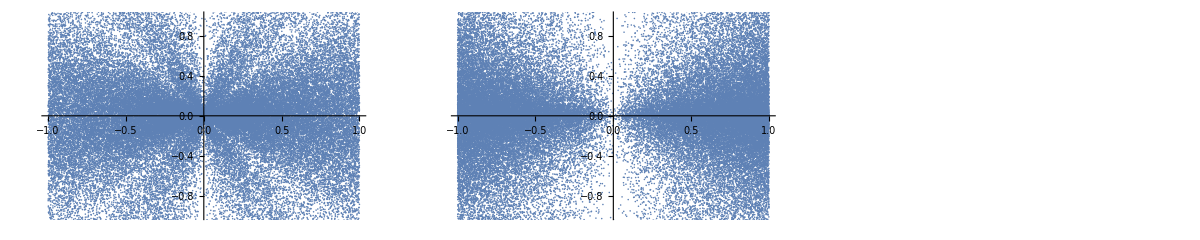

```mathematica
GraphicsGrid[Partition[plotsx1,3]] (* x1 in term of the others*)
```

```mathematica
npoints=100000; (*Nombre de points*)
fx2m[x1_,x4_,x8_]:=(ⅇ^x8 x1 x4-√(x1^2 (-1+ⅇ^x8 (2-ⅇ^x8+x4^2))))/(-1+ⅇ^x8+ⅇ^x8 x4^2);
fx2p[x1_,x4_,x8_]:=(ⅇ^x8 x1 x4+√(x1^2 (-1+ⅇ^x8 (2-ⅇ^x8+x4^2))))/(-1+ⅇ^x8+ⅇ^x8 x4^2); 
range=1;
pointsplusx2=Table[Module[{x,y,z},x=RandomReal[{-range,range}];
y=RandomReal[{-range,range}];
z=RandomReal[{-range,range}];
{x,y,z,fx2m[x,y,z]}],{npoints}];
pointsminusx2=Table[Module[{x,y,z},x=RandomReal[{-range,range}];
y=RandomReal[{-range,range}];
z=RandomReal[{-range,range}];
{x,y,z,fx2p[x,y,z]}],{npoints}];
```

```mathematica
plotsx2=Table[ListPlot[Join[pointsminusx2[[;;,{i,4}]],pointsplusx2[[;;,{i,4}]]],PlotRange->{{-1,1},{-1,1}}],{i,3}];
```

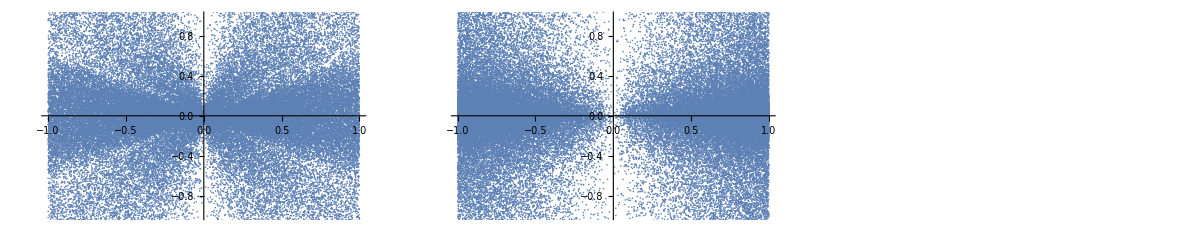

```mathematica
GraphicsGrid[Partition[plotsx2,3]] (* x2 in term of the others*)
```

```mathematica
npoints=100000; (*Nombre de points*)
fx4m[x1_,x2_,x8_]:=x1/x2-(ⅇ^(-x8/2) √(x1^2-(-1+ⅇ^x8) x2^2))/x2;
fx4p[x1_,x2_,x8_]:=x1/x2+(ⅇ^(-x8/2) √(x1^2-(-1+ⅇ^x8) x2^2))/x2; 
range=1;
pointsplusx4=Table[Module[{x,y,z},x=RandomReal[{-range,range}];
y=RandomReal[{-range,range}];
z=RandomReal[{-range,range}];
{x,y,z,fx4m[x,y,z]}],{npoints}];
pointsminusx4=Table[Module[{x,y,z},x=RandomReal[{-range,range}];
y=RandomReal[{-range,range}];
z=RandomReal[{-range,range}];
{x,y,z,fx4p[x,y,z]}],{npoints}];
```

```mathematica
plotsx4=Table[ListPlot[Join[pointsminusx4[[;;,{i,4}]],pointsplusx4[[;;,{i,4}]]],PlotRange->{{-1,1},{-1,1}}],{i,3}];
```

```mathematica
GraphicsGrid[Partition[plotsx4,3]] (* x4 in term of the others*)
```

-Graphics-

```mathematica
npoints=100000; (*Nombre de points*)
fx8[x1_,x2_,x4_]:=Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)];
range=1;
pointsx8=Table[Module[{x,y,z},x=RandomReal[{-range,range}];
y=RandomReal[{-range,range}];
z=RandomReal[{-range,range}];
{x,y,z,fx8[x,y,z]}],{npoints}];
```

```mathematica
plotsx8=Table[ListPlot[pointsx8[[;;,{i,4}]],PlotRange->{{-1,1},{-1,1}}],{i,3}];
```

```mathematica
GraphicsGrid[Partition[plotsx8,3]] (* x8 in term of the others*)
```

-Graphics-

Indeed ! Family of solution for {x1→ free, x2 →(ⅇ^x8 x1 x4±√(x1^2 (-1+ⅇ^x8 (2-ⅇ^x8+x4^2))))/(-1+ⅇ^x8+ⅇ^x8 x4^2), x4 → free, x8 → free, x10->(√2 (x1-x1 x8+x2 x4 x8))/(x2 x8)}

### Recover 4d families

```mathematica
(*x2->0,x4 free,x8 free,x10->±√2 ⅇ^-x8 √(-1+2 ⅇ^x8-ⅇ^(2 x8)+ⅇ^x8 x4^2)*)
```

```mathematica
solx2/.x1->0
```

{{x2→0},{x2→0}}

```mathematica
(solx10/.solx2//FullSimplify)
```

{x10→-(√2 √(-x1^2 (1-(2+x4^2) x8+x8^2)))/(x1 x8),x10→(√2 √(-x1^2 (1-(2+x4^2) x8+x8^2)))/(x1 x8)}

```mathematica
{(√2 √(-(1-(2+x4^2) x8+x8^2)))/x8,(√2 √(-(1-(2+x4^2) x8+x8^2)))/x8}/.x8->Exp[x8]
```

{√2 ⅇ^-x8 √(-1-ⅇ^(2 x8)+ⅇ^x8 (2+x4^2)),√2 ⅇ^-x8 √(-1-ⅇ^(2 x8)+ⅇ^x8 (2+x4^2))}

```mathematica
(*x2 -> free, x4 -> free, x8 -> -Log[1+x4^2], x10->√2 x4}*)
(*x2->0,x4 free,x8 free,x10->±√2 ⅇ^-x8 √(-1+2 ⅇ^x8-ⅇ^(2 x8)+ⅇ^x8 x4^2)*)
```

```mathematica
x8->Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)]/.x1->0//FullSimplify
solx10/.x8->Exp[x8]/.x1->0
```

x8→Log[1/(1+x4^2)]

x10→√2 x4

```mathematica
Exp[x8]*(1+x4^2)-1==0
x10-√2 x4==0
```

-1+ⅇ^x8 (1+x4^2)==0

x10-√2 x4==0

```mathematica
(**)
```

```mathematica
solx10
```

x10→(√2 (x1-x1 x8+x2 x4 x8))/(x2 x8)

```mathematica
pol[1]=(x10 x2 x8-√2(x1-x1 x8+x2 x4 x8))==0
```

x10 x2 x8-√2 (x1-x1 x8+x2 x4 x8)==0

```mathematica
pol[2]=x8(x2^2+(x1-x2 x4)^2)-(x1^2+x2^2)==0
```

-x1^2-x2^2+(x2^2+(x1-x2 x4)^2) x8==0

```mathematica
{pol[1],pol[2]}/.x1->0
```

{x10 x2 x8-√2 x2 x4 x8==0,-x2^2+(x2^2+x2^2 x4^2) x8==0}

```mathematica
Solve[({pol[1],pol[2]}/.x1->0),{x4,x10}]
Solve[({pol[1],pol[2]}/.x1->0),{x2,x10}]
```

{{x4→-(√(1-x8))/(√x8),x10→-(√2 √(1-x8))/(√x8)},{x4→(√(1-x8))/(√x8),x10→(√2 √(1-x8))/(√x8)}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→0}}

```mathematica
solx10
solx8
solx2
```

x10→(√2 (x1-x1 x8+x2 x4 x8))/(x2 x8)

{{x8→(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)}}

{{x2→(x1 x4 x8-√(x1^2 (-1+(2+x4^2-x8) x8)))/(-1+x8+x4^2 x8)},{x2→(x1 x4 x8+√(x1^2 (-1+(2+x4^2-x8) x8)))/(-1+x8+x4^2 x8)}}

```mathematica
pol[3]=(x2(-1+x8+x4^2 x8)-x1 x4 x8)^2-x1^2 (-1+(2+x4^2-x8) x8)==0//Simplify
```

x1^2+(x1 x4 x8-x2 (-1+x8+x4^2 x8))^2==x1^2 (2+x4^2-x8) x8

```mathematica
pol[1]
pol[2]
pol[3]
```

x10 x2 x8-√2 (x1-x1 x8+x2 x4 x8)==0

-x1^2-x2^2+(x2^2+(x1-x2 x4)^2) x8==0

x1^2+(x1 x4 x8-x2 (-1+x8+x4^2 x8))^2==x1^2 (2+x4^2-x8) x8

```mathematica
Solve[pol[1]&&pol[2],{x8,x10}]/.x1->0//Simplify//Union
```

{{x8→1/(1+x4^2),x10→√2 x4}}

```mathematica
Simplify[Solve[pol[1]&&pol[2],{x2,x10}],x1>0]/.x1->0
```

{{x2→0,x10→-(√(-2+2 (2+x4^2) x8-2 x8^2))/x8},{x2→0,x10→(√(-2+2 (2+x4^2) x8-2 x8^2))/x8}}

```mathematica
(*x2 -> free, x4 -> free, x8 -> -Log[1+x4^2], x10->√2 x4}*)
(*x2->0,x4 free,x8 free,x10->±√2 ⅇ^-x8 √(-1+2 ⅇ^x8-ⅇ^(2 x8)+ⅇ^x8 x4^2)*)
```

```mathematica
pol[3]/.Solve[pol[1]&&pol[2]]//FullSimplify
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
pol[1]//Expand
pol[2]//Expand
pol[3]//Expand
```

-√2 x1+√2 x1 x8+x10 x2 x8-√2 x2 x4 x8==0

-x1^2-x2^2+x1^2 x8+x2^2 x8-2 x1 x2 x4 x8+x2^2 x4^2 x8==0

x1^2+x2^2-2 x2^2 x8+2 x1 x2 x4 x8-2 x2^2 x4^2 x8+x2^2 x8^2-2 x1 x2 x4 x8^2+x1^2 x4^2 x8^2+2 x2^2 x4^2 x8^2-2 x1 x2 x4^3 x8^2+x2^2 x4^4 x8^2==2 x1^2 x8+x1^2 x4^2 x8-x1^2 x8^2

```mathematica
Solve[pol[1],x10]
```

{{x10→-(√2 (-x1+x1 x8-x2 x4 x8))/(x2 x8)}}

### Try to characterise the manifold

```mathematica
solx10/.x8->(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)//FullSimplify
```

x10→(√2 x4 (-x1^2+x2^2+x1 x2 x4))/(x1^2+x2^2)

```mathematica
x8->Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)]
```

x8→Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)]

```mathematica
M0=SparseArray[(M01//Normal)/.x10->(√2 x4 (-x1^2+x2^2+x1 x2 x4))/(x1^2+x2^2)/.x8->Log[(x1^2+x2^2)/(x2^2+(x1-x2 x4)^2)]//FullSimplify]
```

SparseArray[…]

```mathematica
ds2=1/8 Tr[Dt[M0].eta.Dt[M0].eta]//Simplify
```

-1/(2 (x1^2+x2^2)^2)((x2^6+x1^4 (2+x2^2)-4 x1^3 x2 x4-4 x1 x2^3 x4+2 x2^4 (1+x4^2)+x2^2 x4^2 (4+x4^2)+2 x1^2 x2^2 (2+x2^2+x4^2)) Dt[x1]^2+(x1^6+2 x2^4+4 x1^3 x2 x4+4 x1 x2^3 x4+2 x1^4 (1+x2^2+x4^2)+x1^2 (x2^4+2 x2^2 (2+x4^2)+x4^2 (4+x4^2))) Dt[x2]^2-2 x1 (x1^2+x2^2) (x1^2+x2^2-x4^2) Dt[x2] Dt[x4]+2 (x1^2+x2^2)^2 Dt[x4]^2-2 Dt[x1] ((x1^5 x2-2 x1^4 x4+2 x2^4 x4+2 x1^3 x2 (x2^2+x4^2)+x1 x2 (x2^4+4 x4^2+2 x2^2 x4^2+x4^4)) Dt[x2]-x2 (x1^2+x2^2) (x1^2+x2^2-x4^2) Dt[x4]))

```mathematica
coord={x1,x2,x4};
metric=Table[If[i===j,1,1/2]Coefficient[ds2,Dt[coord][[i]]Dt[coord][[j]]],{i,Length[coord]},{j,Length[coord]}]//FullSimplify;
metric //MatrixForm
```

(-((2+x2^2) (x1^2+x2^2)^2-4 x1 x2 (x1^2+x2^2) x4+2 x2^2 (2+x1^2+x2^2) x4^2+x2^2 x4^4)/(2 (x1^2+x2^2)^2) | (x1 x2 (x1^2+x2^2)^2+2 (-x1^4+x2^4) x4+2 x1 x2 (2+x1^2+x2^2) x4^2+x1 x2 x4^4)/(2 (x1^2+x2^2)^2) | 1/2 x2 (-1+x4^2/(x1^2+x2^2))
(x1 x2 (x1^2+x2^2)^2+2 (-x1^4+x2^4) x4+2 x1 x2 (2+x1^2+x2^2) x4^2+x1 x2 x4^4)/(2 (x1^2+x2^2)^2) | -((2+x1^2) (x1^2+x2^2)^2+4 x1 x2 (x1^2+x2^2) x4+2 x1^2 (2+x1^2+x2^2) x4^2+x1^2 x4^4)/(2 (x1^2+x2^2)^2) | 1/2 x1 (1-x4^2/(x1^2+x2^2))
1/2 x2 (-1+x4^2/(x1^2+x2^2)) | 1/2 x1 (1-x4^2/(x1^2+x2^2)) | -1)

```mathematica
Det[metric]//FullSimplify
```

-(x1^4+(x2^2+x4^2)^2+2 x1^2 (2+x2^2+x4^2)+4 (x2^2+2 x4^2))/(4 (x1^2+x2^2))

```mathematica
newcoo={θ,ϕ,r};
Yangles={r Cos[θ]Cos[ϕ],r Cos[θ]Sin[ϕ],r Sin[θ]};
```

```mathematica
Det[metric]/.{x1->Yangles[[1]],x2->Yangles[[2]],x4->Yangles[[3]]}//FullSimplify
```

1-1/4 (8+r^2) Sec[θ]^2

```mathematica
Jac=Table[D[Yangles[[m]],newcoo[[n]]],{m,3},{n,3}];
metricNew=Simplify[Transpose[Jac].metric.Jac/.{x1->Yangles[[1]],x2->Yangles[[2]],x4->Yangles[[3]]}]
```

{{-r^2,1/2 r^3 Cos[θ],0},{1/2 r^3 Cos[θ],-1/2 r^2 (3+r^2-Cos[2 θ]),-1/2 r^2 Sin[θ]},{0,-1/2 r^2 Sin[θ],-1}}

```mathematica
MatrixForm[metricNew]
```

(-r^2 | 1/2 r^3 Cos[θ] | 0
1/2 r^3 Cos[θ] | -1/2 r^2 (3+r^2-Cos[2 θ]) | -1/2 r^2 Sin[θ]
0 | -1/2 r^2 Sin[θ] | -1)

```mathematica
newcoo={θ,ϕ,r};
```

```mathematica
gInv=Inverse[metricNew]//FullSimplify;
g=metricNew;
```

```mathematica
christoffel=Table[1/2 Sum[gInv[[i,s]] (D[g[[s,j]],newcoo[[k]]]+D[g[[s,k]],newcoo[[j]]]-D[g[[j,k]],newcoo[[s]]]),{s,1,3}],{i,1,3},{j,1,3},{k,1,3}]//FullSimplify;
```

```mathematica
riemann=Table[D[christoffel[[i,j,k]],newcoo[[l]]]-D[christoffel[[i,j,l]],newcoo[[k]]]+Sum[christoffel[[m,j,k]] christoffel[[i,m,l]]-christoffel[[m,j,l]] christoffel[[i,m,k]],{m,1,3}],{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
```

```mathematica
ricci=Table[Sum[riemann[[m,i,m,j]],{m,1,3}],{i,1,3},{j,1,3}];
```

```mathematica
ricciScalar=Simplify[Sum[gInv[[i,j]] ricci[[i,j]],{i,1,3},{j,1,3}]];
```

```mathematica
ricciScalar
```

(4 (-16-35 r^2-3 r^4+r^2 (32+3 r^2) Cos[2 θ]-3 r^2 Cos[4 θ]))/(r^2 (6+r^2-2 Cos[2 θ])^2)

## ExFT scalar matrix and 6d fields

```mathematica
MExFT=Simplify[eta33114.U.eta33114.SparseArray[Simplify[Normal[M02]/.{aa->0,bb->0}]].Transpose[eta33114.U.eta33114]];//Timing
```

{42.3962,Null}

### Metric

#### Computations

g^-1g^mn

```mathematica
invmetrictemp=Simplify[MExFT[[8,8]]MExFT[[4;;6,4;;6]]- Table[MExFT[[8,m]]MExFT[[8,n]],{m,4,6},{n,4,6}]];
dettemp=Factor[Det[invmetrictemp]]
Simplify[dettemp^(1/4)]
```

(-1+y[1]^2+y[2]^2+y[3]^2)^4 (1+x3^2 y[1]^2+x1^2 y[2]^2+x3^2 y[2]^2-2 x1 x3 y[1] y[3]+x1^2 y[3]^2)^2

Abs[-1+y[1]^2+y[2]^2+y[3]^2] ((1+x3^2 (y[1]^2+y[2]^2)-2 x1 x3 y[1] y[3]+x1^2 (y[2]^2+y[3]^2))^2)^(1/4)

g^mn

```mathematica
invmetricy=Simplify[invmetrictemp/(√(1+x3^2 (y[1]^2+y[2]^2)-2 x1 x3 y[1] y[3]+x1^2 (y[2]^2+y[3]^2)) (1-y[1]^2-y[2]^2-y[3]^2))];
```

```mathematica
Det[invmetricy]/Det[ih]//FullSimplify
```

√(1+x3^2 (y[1]^2+y[2]^2)-2 x1 x3 y[1] y[3]+x1^2 (y[2]^2+y[3]^2))

Warp factor Δ

```mathematica
Δ2y=1/(√(1+x3^2 (y[1]^2+y[2]^2)-2 x1 x3 y[1] y[3]+x1^2 (y[2]^2+y[3]^2)));
```

```mathematica
Δ2y^-1 invmetricy//MatrixForm//FullSimplify
```

(1-y[1]^2+x3 y[2] (x3 (2+x1^2+x3^2) y[2]-2 x1 √(1-y[1]^2-y[2]^2-y[3]^2)) | x1 y[3] (x3 (2+x1^2+x3^2) y[2]-x1 √(1-y[1]^2-y[2]^2-y[3]^2))+y[1] (-((1+(2+x1^2) x3^2+x3^4) y[2])+x1 x3 √(1-y[1]^2-y[2]^2-y[3]^2)) | -y[1] y[3]+y[2] (-x1 x3 (2+x1^2+x3^2) y[2]+x1^2 √(1-y[1]^2-y[2]^2-y[3]^2)-x3^2 √(1-y[1]^2-y[2]^2-y[3]^2))
x1 y[3] (x3 (2+x1^2+x3^2) y[2]-x1 √(1-y[1]^2-y[2]^2-y[3]^2))+y[1] (-((1+(2+x1^2) x3^2+x3^4) y[2])+x1 x3 √(1-y[1]^2-y[2]^2-y[3]^2)) | 1-y[2]^2+(2+x1^2+x3^2) (x3 y[1]-x1 y[3])^2 | x1 x3 (2+x1^2+x3^2) y[1] y[2]-(1+x1^4+x1^2 (2+x3^2)) y[2] y[3]+x3^2 y[1] √(1-y[1]^2-y[2]^2-y[3]^2)-x1 x3 y[3] √(1-y[1]^2-y[2]^2-y[3]^2)
-y[1] y[3]+y[2] (-x1 x3 (2+x1^2+x3^2) y[2]+x1^2 √(1-y[1]^2-y[2]^2-y[3]^2)-x3^2 √(1-y[1]^2-y[2]^2-y[3]^2)) | x1 x3 (2+x1^2+x3^2) y[1] y[2]-(1+x1^4+x1^2 (2+x3^2)) y[2] y[3]+x3^2 y[1] √(1-y[1]^2-y[2]^2-y[3]^2)-x1 x3 y[3] √(1-y[1]^2-y[2]^2-y[3]^2) | 1-y[3]^2+x1 y[2] (x1^3 y[2]+x1 (2+x3^2) y[2]+2 x3 √(1-y[1]^2-y[2]^2-y[3]^2)))

Change of coordinates : (y_1,y_2,y_3) → (θ,ϕ1,ϕ2)

```mathematica
angles={θ,ϕ1,ϕ2};
Yangles={Cos[θ]Cos[ϕ1],Cos[θ]Sin[ϕ1],Sin[θ]Cos[ϕ2]};
Jac=Table[D[Yangles[[m]],angles[[n]]],{m,3},{n,3}];
invmetricangles=Simplify[Inverse[Jac].invmetricy.Transpose[Inverse[Jac]]/.{y[1]->Yangles[[1]],y[2]->Yangles[[2]],y[3]->Yangles[[3]]}];
```

```mathematica
Det[invmetricangles]//FullSimplify
```

$Aborted

```mathematica
invmetricangles//MatrixForm
```

((-Cos[ϕ1]^4 Cot[θ]^2+Cos[ϕ1]^2 (Csc[θ]^2-2 Cot[θ]^2 Sin[ϕ1]^2)+Sin[ϕ1]^2 (x1^2 (2+x1^2+x3^2) Cos[ϕ2]^2+Csc[θ]^2-Cot[θ]^2 Sin[ϕ1]^2)-x1^2 Abs[Sin[ϕ2]] Cos[ϕ2] Sin[2 ϕ1])/(√(1+1/2 Cos[θ]^2 (x1^2+2 x3^2-x1^2 Cos[2 ϕ1])+x1^2 Cos[ϕ2]^2 Sin[θ]^2-x1 x3 Cos[ϕ1] Cos[ϕ2] Sin[2 θ])) | (x1 ((2+x1^2+x3^2) Cos[ϕ2] Sin[ϕ1] (x3-x1 Cos[ϕ1] Cos[ϕ2] Tan[θ])-Abs[Sin[ϕ2]] (x3 Cos[ϕ1]-x1 Cos[ϕ1]^2 Cos[ϕ2] Tan[θ]+x1 Cos[ϕ2] Sin[ϕ1]^2 Tan[θ])))/(√(1+1/2 Cos[θ]^2 (x1^2+2 x3^2-x1^2 Cos[2 ϕ1])+x1^2 Cos[ϕ2]^2 Sin[θ]^2-x1 x3 Cos[ϕ1] Cos[ϕ2] Sin[2 θ])) | (x1 Sin[ϕ1] (-Abs[Sin[ϕ2]] (x3+x1 Cos[ϕ1] Cos[ϕ2] Cot[θ]) Cot[ϕ2]+x1 Abs[Sin[ϕ2]] Cos[ϕ1] Cot[θ] Sin[ϕ2]-x1 (2+x1^2+x3^2) Cos[ϕ2] Cot[θ] Sin[ϕ1] Sin[ϕ2]))/(√(1+1/2 Cos[θ]^2 (x1^2+2 x3^2-x1^2 Cos[2 ϕ1])+x1^2 Cos[ϕ2]^2 Sin[θ]^2-x1 x3 Cos[ϕ1] Cos[ϕ2] Sin[2 θ]))
(x1 ((2+x1^2+x3^2) Cos[ϕ2] Sin[ϕ1] (x3-x1 Cos[ϕ1] Cos[ϕ2] Tan[θ])-Abs[Sin[ϕ2]] (x3 Cos[ϕ1]-x1 Cos[ϕ1]^2 Cos[ϕ2] Tan[θ]+x1 Cos[ϕ2] Sin[ϕ1]^2 Tan[θ])))/(√(1+1/2 Cos[θ]^2 (x1^2+2 x3^2-x1^2 Cos[2 ϕ1])+x1^2 Cos[ϕ2]^2 Sin[θ]^2-x1 x3 Cos[ϕ1] Cos[ϕ2] Sin[2 θ])) | (x3^2 (2+x1^2+x3^2) Cos[ϕ1]^4+Sec[θ]^2 Sin[ϕ1]^2+2 x3^2 Sin[ϕ1]^4+x1^2 x3^2 Sin[ϕ1]^4+x3^4 Sin[ϕ1]^4+x3^2 Sin[2 ϕ1]^2-2 x1 x3 (2+x1^2+x3^2) Cos[ϕ1]^3 Cos[ϕ2] Tan[θ]-2 x1 x3 (2+x1^2+x3^2) Cos[ϕ1] Cos[ϕ2] Sin[ϕ1]^2 Tan[θ]+2 x1 Abs[Sin[ϕ2]] Sin[ϕ1] Tan[θ] (-x3+x1 Cos[ϕ1] Cos[ϕ2] Tan[θ])+Cos[ϕ1]^2 (Sec[θ]^2+2 x3^2 (x1^2+x3^2) Sin[ϕ1]^2+x1^2 (2+x1^2+x3^2) Cos[ϕ2]^2 Tan[θ]^2))/(√(1+1/2 Cos[θ]^2 (x1^2+2 x3^2-x1^2 Cos[2 ϕ1])+x1^2 Cos[ϕ2]^2 Sin[θ]^2-x1 x3 Cos[ϕ1] Cos[ϕ2] Sin[2 θ])) | (1/4 Abs[Sin[ϕ2]] ((2 x1^2-4 x3^2+x1^2 Cos[2 ϕ1-2 ϕ2]+x1^2 Cos[2 (ϕ1+ϕ2)]) Csc[ϕ2]-4 x1 x3 Cos[2 θ] Cos[ϕ1] Cot[ϕ2] Csc[θ] Sec[θ])+x1 (2+x1^2+x3^2) (x1 Cos[ϕ1] Cos[ϕ2]-x3 Cot[θ]) Sin[ϕ1] Sin[ϕ2])/(√(1+1/2 Cos[θ]^2 (x1^2+2 x3^2-x1^2 Cos[2 ϕ1])+x1^2 Cos[ϕ2]^2 Sin[θ]^2-x1 x3 Cos[ϕ1] Cos[ϕ2] Sin[2 θ]))
(x1 Sin[ϕ1] (-Abs[Sin[ϕ2]] (x3+x1 Cos[ϕ1] Cos[ϕ2] Cot[θ]) Cot[ϕ2]+x1 Abs[Sin[ϕ2]] Cos[ϕ1] Cot[θ] Sin[ϕ2]-x1 (2+x1^2+x3^2) Cos[ϕ2] Cot[θ] Sin[ϕ1] Sin[ϕ2]))/(√(1+1/2 Cos[θ]^2 (x1^2+2 x3^2-x1^2 Cos[2 ϕ1])+x1^2 Cos[ϕ2]^2 Sin[θ]^2-x1 x3 Cos[ϕ1] Cos[ϕ2] Sin[2 θ])) | (1/4 Abs[Sin[ϕ2]] ((2 x1^2-4 x3^2+x1^2 Cos[2 ϕ1-2 ϕ2]+x1^2 Cos[2 (ϕ1+ϕ2)]) Csc[ϕ2]-4 x1 x3 Cos[2 θ] Cos[ϕ1] Cot[ϕ2] Csc[θ] Sec[θ])+x1 (2+x1^2+x3^2) (x1 Cos[ϕ1] Cos[ϕ2]-x3 Cot[θ]) Sin[ϕ1] Sin[ϕ2])/(√(1+1/2 Cos[θ]^2 (x1^2+2 x3^2-x1^2 Cos[2 ϕ1])+x1^2 Cos[ϕ2]^2 Sin[θ]^2-x1 x3 Cos[ϕ1] Cos[ϕ2] Sin[2 θ])) | (Csc[ϕ2]^2 (Cos[ϕ1]^4 (Csc[θ]^2-Cos[ϕ2]^2 Csc[θ]^4+x1^2 (2+x1^2+x3^2) Cot[θ]^2 Sin[ϕ1]^2)+Sin[ϕ1]^2 (x1^2 (2+x1^2+x3^2) Cos[ϕ2]^4 Cot[θ]^2+Sin[ϕ1]^2 (Csc[θ]^2+x1^2 (2+x1^2+x3^2) Cot[θ]^2 Sin[ϕ1]^2)-Cos[ϕ2]^2 (Sin[ϕ1]^2+Cot[θ]^4 Sin[ϕ1]^2+Cot[θ]^2 (-Csc[θ]^2+2 (1+x1^4+x1^2 (2+x3^2)) Sin[ϕ1]^2)))+Cos[ϕ1]^2 (2 Sin[ϕ1]^2 (Csc[θ]^2+x1^2 (2+x1^2+x3^2) Cot[θ]^2 Sin[ϕ1]^2)-Cos[ϕ2]^2 (2 Sin[ϕ1]^2+2 Cot[θ]^4 Sin[ϕ1]^2+Cot[θ]^2 (-Csc[θ]^2+2 (2+x1^4+x1^2 (2+x3^2)) Sin[ϕ1]^2)))+2 x1 Abs[Sin[ϕ2]] Cot[θ] (x3+x1 Cos[ϕ1] Cos[ϕ2] Cot[θ]) Sin[ϕ1] Sin[ϕ2]^2))/(√(1+1/2 Cos[θ]^2 (x1^2+2 x3^2-x1^2 Cos[2 ϕ1])+x1^2 Cos[ϕ2]^2 Sin[θ]^2-x1 x3 Cos[ϕ1] Cos[ϕ2] Sin[2 θ])))

STOPPED HERE

```mathematica
Δ2=ⅇ^(-η/2)/(√(1+(-1+ⅇ^(-2 η)+ζ^2) Cos[α]^2));
```

```mathematica
invmet=Δ2({{1, 0, 0}, {0, ⅇ^(-2 η)/Cos[α]^2 (ⅇ^(2 η)+Cos[α]^2((1+ⅇ^(2 η)ζ^2)^2-ⅇ^(2 η))), -ⅇ^(2 η) ζ^2}, {0, -ⅇ^(2 η) ζ^2, (ⅇ^(2 η)+(1-ⅇ^(2 η))Cos[α]^2)1/Sin[α]^2}});
```

```mathematica
invmet-invmetricangles//FullSimplify//Flatten//Union
```

{0,(ⅇ^(3 η/2) ζ^2 (-1+Abs[Sin[γ]] Csc[γ]))/(√(1+(-1+ⅇ^(-2 η)+ζ^2) Cos[α]^2))}

```mathematica
met=FullSimplify[Inverse[invmet]];
met//MatrixForm
```

(ⅇ^(η/2) √(1+(-1+ⅇ^(-2 η)+ζ^2) Cos[α]^2) | 0 | 0
0 | (4 ⅇ^(η/2) Cos[α]^2 (Cos[α]^2+ⅇ^(2 η) (1+(-1+ζ^2) Cos[α]^2)) (Cos[α]^2+ⅇ^(2 η) Sin[α]^2))/(√(1+(-1+ⅇ^(-2 η)+ζ^2) Cos[α]^2) (1+Cos[2 α]+ⅇ^(2 η) (1+ζ^2+(-1+ζ^2) Cos[2 α]))^2) | (4 ⅇ^(5 η/2) ζ^2 Cos[α]^2 (Cos[α]^2+ⅇ^(2 η) (1+(-1+ζ^2) Cos[α]^2)) Sin[α]^2)/(√(1+(-1+ⅇ^(-2 η)+ζ^2) Cos[α]^2) (1+Cos[2 α]+ⅇ^(2 η) (1+ζ^2+(-1+ζ^2) Cos[2 α]))^2)
0 | (4 ⅇ^(5 η/2) ζ^2 Cos[α]^2 (Cos[α]^2+ⅇ^(2 η) (1+(-1+ζ^2) Cos[α]^2)) Sin[α]^2)/(√(1+(-1+ⅇ^(-2 η)+ζ^2) Cos[α]^2) (1+Cos[2 α]+ⅇ^(2 η) (1+ζ^2+(-1+ζ^2) Cos[2 α]))^2) | (4 ⅇ^(-3 η/2) (ⅇ^(2 η)+(1+ⅇ^(4 η) ζ^4+ⅇ^(2 η) (-1+2 ζ^2)) Cos[α]^2) (Cos[α]^2+ⅇ^(2 η) (1+(-1+ζ^2) Cos[α]^2)) Sin[α]^2)/(√(1+(-1+ⅇ^(-2 η)+ζ^2) Cos[α]^2) (1+Cos[2 α]+ⅇ^(2 η) (1+ζ^2+(-1+ζ^2) Cos[2 α]))^2))

```mathematica
metric=1/Δ2({{1, 0, 0}, {0, Δ2^4 Cos[α]^2(Cos[α]^2+ⅇ^(2 η)Sin[α]^2), Δ2^4 ⅇ^(2 η)ζ^2 Cos[α]^2 Sin[α]^2}, {0, Δ2^4 ⅇ^(2 η) ζ^2 Cos[α]^2 Sin[α]^2, Δ2^4 ⅇ^(-2 η)Sin[α]^2(ⅇ^(2 η)+Cos[α]^2((1+ⅇ^(2 η)ζ^2)^2-ⅇ^(2 η)))}});
```

```mathematica
metric-met//FullSimplify//Flatten//Union
```

{0}

### Dilaton

ℳ^00

```mathematica
MExFT[[8,8]]
Det[ih]//Simplify
```

1-y[1]^2-y[2]^2-y[3]^2

1-y[1]^2-y[2]^2-y[3]^2

```mathematica
expPhi=Δ2;
```

### b field and field-strength H

```mathematica
Hy= β/(4 √Det[ih])LeviCivitaTensor[3];
H=β/4 Cos[α]Sin[α]LeviCivitaTensor[3];
```

#### Computations

b_mn

```mathematica
bfieldy=-1/MExFT[[8,8]] LeviCivitaTensor[3].MExFT[[8,4;;6]];
bfieldy-β/4 1/(√Det[ih])LeviCivitaTensor[3].xi//Normal//Simplify//Flatten//Union
```

{0}

H_mnp

```mathematica
Hy=FullSimplify[Table[D[bfieldy[[n,p]],y[m]]+D[bfieldy[[m,n]],y[p]]+D[bfieldy[[p,m]],y[n]],{m,3},{n,3},{p,3}]/.rulexi];
Hy- β/(4 √Det[ih])LeviCivitaTensor[3]//FullSimplify//Flatten//Union
```

{0}

```mathematica
H=β/4 Cos[α]Sin[α]LeviCivitaTensor[3];
```

### Vectors A and field-strengths F

```mathematica
Ay=Δ2y^2({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {√2 ⅇ^η ζ (y[2]-(y[1] y[3])/(√(1-y[1]^2-y[2]^2-y[3]^2))), √2 ⅇ^η ζ (-y[1]-(y[2] y[3])/(√(1-y[1]^2-y[2]^2-y[3]^2))), (√2 ⅇ^η ζ (-1+y[1]^2+y[2]^2))/(√(1-y[1]^2-y[2]^2-y[3]^2))}});
A=ⅇ^η ζ √2 Δ2^2({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, - Cos[α]^2, Sin[α]^2}});
Fy=FullSimplify[Table[D[Ay[[alpha,n]],y[m]]-D[Ay[[alpha,m]],y[n]],{alpha,4},{m,3},{n,3}]];
F=FullSimplify[Table[D[A[[alpha,n]],{α,β2,γ}[[m]]]-D[A[[alpha,m]],{α,β2,γ}[[n]]],{alpha,4},{m,3},{n,3}]];
```

#### Computations

A_m^α

```mathematica
Atemp=Simplify[MExFT[[8,8]]MExFT[[9;;12,4;;6]]- Table[MExFT[[8,alpha]]MExFT[[8,m]],{alpha,9,12},{m,4,6}]];
Ay=FullSimplify[1/Det[invmetricy] Atemp.Inverse[invmetricy]];
```

```mathematica
1/Δ2y 1/Δ2y Ay//FullSimplify//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
√2 ⅇ^η ζ (y[2]-(y[1] y[3])/(√(1-y[1]^2-y[2]^2-y[3]^2))) | √2 ⅇ^η ζ (-y[1]-(y[2] y[3])/(√(1-y[1]^2-y[2]^2-y[3]^2))) | (√2 ⅇ^η ζ (-1+y[1]^2+y[2]^2))/(√(1-y[1]^2-y[2]^2-y[3]^2)))

Change of coordinates : (y_1,y_2,y_3) → (α, β2,γ)

```mathematica
Aangles=Simplify[Ay.Jac/.{y[1]->Yangles[[1]],y[2]->Yangles[[2]],y[3]->Yangles[[3]]}];
Aangles//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | -(2 √2 ⅇ^(2 η) ζ Cos[α]^2)/(1+ⅇ^(2 η) (1+ζ^2)+(1+ⅇ^(2 η) (-1+ζ^2)) Cos[2 α]) | (2 √2 ⅇ^(2 η) ζ Sin[α]^2 Sin[γ])/(Abs[Sin[γ]] (1+ⅇ^(2 η) (1+ζ^2)+(1+ⅇ^(2 η) (-1+ζ^2)) Cos[2 α])))

```mathematica
A=ⅇ^η ζ √2 Δ2^2({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, - Cos[α]^2, Sin[α]^2}});
A-Aangles//FullSimplify//Flatten//Union
```

{0,(2 √2 ⅇ^(2 η) ζ Abs[Csc[γ]] Sin[α]^2 (Abs[Sin[γ]]-Sin[γ]))/(1+Cos[2 α]+ⅇ^(2 η) (1+ζ^2+(-1+ζ^2) Cos[2 α]))}

F_mn^α

```mathematica
F=FullSimplify[Table[D[A[[alpha,n]],{α,β2,γ}[[m]]]-D[A[[alpha,m]],{α,β2,γ}[[n]]],{alpha,4},{m,3},{n,3}]];
F[[1;;3,All,All]]//Flatten//Union
F[[4,All,All]] 1/Δ2^4//MatrixForm//FullSimplify
```

{0}

(0 | √2 ⅇ^(2 η) ζ Sin[2 α] | √2 ζ (1+ⅇ^(2 η) ζ^2) Sin[2 α]
-√2 ⅇ^(2 η) ζ Sin[2 α] | 0 | 0
-√2 ζ (1+ⅇ^(2 η) ζ^2) Sin[2 α] | 0 | 0)

```mathematica
Fy=FullSimplify[Table[D[Ay[[alpha,n]],y[m]]-D[Ay[[alpha,m]],y[n]],{alpha,4},{m,3},{n,3}]];
Fy[[1;;3,All,All]]//Flatten//Union
Fy[[4,All,All]] 1/Δ2y^4//MatrixForm//FullSimplify
```

{0}

(0 | -2 √2 ⅇ^(2 η) ζ | (2 √2 ζ (1+ⅇ^(2 η) ζ^2) y[1])/(√(1-y[1]^2-y[2]^2-y[3]^2))
2 √2 ⅇ^(2 η) ζ | 0 | (2 √2 ζ (1+ⅇ^(2 η) ζ^2) y[2])/(√(1-y[1]^2-y[2]^2-y[3]^2))
-(2 √2 ζ (1+ⅇ^(2 η) ζ^2) y[1])/(√(1-y[1]^2-y[2]^2-y[3]^2)) | -(2 √2 ζ (1+ⅇ^(2 η) ζ^2) y[2])/(√(1-y[1]^2-y[2]^2-y[3]^2)) | 0)

### Dual b field and dual field-strength

```mathematica
Htilde=(2+2 ⅇ^(2 η) (1+2 k) ζ^2)Cos[α]  Sin[α] Δ2^4 LeviCivitaTensor[3];
Htildey=(2+2 ⅇ^(2 η) (1+2 k) ζ^2)Δ2y^4/(√Det[ih])LeviCivitaTensor[3];
```

#### Computations

btilde_mn

```mathematica
btildetemp=Simplify[MExFT[[8,8]]MExFT[[4;;6,1;;3]]- Table[MExFT[[8,m]]MExFT[[8,n]],{m,4,6},{n,1,3}]];
btildetruey=Simplify[1/Det[invmetricy] Inverse[invmetricy].Simplify[btildetemp-1/2 Table[Sum[Atemp[[alpha,m]]Ay[[alpha,n]],{alpha,4}],{m,3},{n,3}]]];
```

```mathematica
btildey=2 1/(√Det[ih])LeviCivitaTensor[3].xi+1/(√Det[ih]) Δ2y^2 ⅇ^η(-1+ⅇ^(-2 η)+ζ^2)({{0, -(y[1]^2+y[2]^2) y[3], (-1+y[1]^2+y[2]^2) y[2]}, {(y[1]^2+y[2]^2) y[3], 0, -y[1] (-1+y[1]^2+y[2]^2)}, {-y[2] (-1+y[1]^2+y[2]^2), (-1+y[1]^2+y[2]^2) y[1], 0}});
btildey-btildetruey//FullSimplify//Flatten//Union
```

{0,2 (1/(√(1-y[1]^2-y[2]^2-y[3]^2))-√(-1/(-1+y[1]^2+y[2]^2+y[3]^2))) x[1][y[1],y[2],y[3]],2 (-1/(√(1-y[1]^2-y[2]^2-y[3]^2))+√(-1/(-1+y[1]^2+y[2]^2+y[3]^2))) x[1][y[1],y[2],y[3]],2 (1/(√(1-y[1]^2-y[2]^2-y[3]^2))-√(-1/(-1+y[1]^2+y[2]^2+y[3]^2))) x[2][y[1],y[2],y[3]],2 (-1/(√(1-y[1]^2-y[2]^2-y[3]^2))+√(-1/(-1+y[1]^2+y[2]^2+y[3]^2))) x[2][y[1],y[2],y[3]],2 (1/(√(1-y[1]^2-y[2]^2-y[3]^2))-√(-1/(-1+y[1]^2+y[2]^2+y[3]^2))) x[3][y[1],y[2],y[3]],2 (-1/(√(1-y[1]^2-y[2]^2-y[3]^2))+√(-1/(-1+y[1]^2+y[2]^2+y[3]^2))) x[3][y[1],y[2],y[3]]}

Change of coordinates

```mathematica
btildeangles=Simplify[(Transpose[Jac].(btildey/.{ x[1][y[1],y[2],y[3]]->x[1],x[2][y[1],y[2],y[3]]->x[2],x[3][y[1],y[2],y[3]]->x[3]}).Jac)/.{y[1]->Yangles[[1]],y[2]->Yangles[[2]],y[3]->Yangles[[3]]}];
btildeangles//FullSimplify//MatrixForm
```

(0 | -2 Cos[α] Csc[γ] Sign[Sin[γ]] (Cos[γ] Cot[α] (Cos[β2] x[1]+Sin[β2] x[2])+x[3]) | 2 Sign[Sin[γ]] Sin[α] (Sin[β2] x[1]-Cos[β2] x[2])
2 Cos[α] Csc[γ] Sign[Sin[γ]] (Cos[γ] Cot[α] (Cos[β2] x[1]+Sin[β2] x[2])+x[3]) | 0 | 1/2 Sign[Sin[γ]] (-((1+ⅇ^(2 η) (-1+ζ^2)) Sin[2 α]^2)/(1+Cos[2 α]+ⅇ^(2 η) (1+ζ^2+(-1+ζ^2) Cos[2 α]))-4 Cos[α] (Cos[β2] x[1]+Sin[β2] x[2]))
2 Sign[Sin[γ]] Sin[α] (-Sin[β2] x[1]+Cos[β2] x[2]) | 1/2 Sign[Sin[γ]] (((1+ⅇ^(2 η) (-1+ζ^2)) Sin[2 α]^2)/(1+Cos[2 α]+ⅇ^(2 η) (1+ζ^2+(-1+ζ^2) Cos[2 α]))+4 Cos[α] (Cos[β2] x[1]+Sin[β2] x[2])) | 0)

Htilde_mnp

```mathematica
Htildeypart1=FullSimplify[Table[D[btildey[[n,p]],y[m]]+D[btildey[[m,n]],y[p]]+D[btildey[[p,m]],y[n]],{m,3},{n,3},{p,3}]/.rulexi];
Htildeypart1[[1,2,3]] Δ2y^-4//FullSimplify
```

(2 (1+ⅇ^(2 η) ζ^2))/(√(1-y[1]^2-y[2]^2-y[3]^2))

```mathematica
Htildeypart2=FullSimplify[Table[Sum[Ay[[alpha,m]]Fy[[alpha,n,p]]+Ay[[alpha,p]]Fy[[alpha,m,n]]+Ay[[alpha,n]]Fy[[alpha,p,m]],{alpha,4}],{m,3},{n,3},{p,3}]];
Htildeypart2[[1,2,3]] Δ2y^-4//FullSimplify
```

(4 ⅇ^(2 η) ζ^2)/(√(1-y[1]^2-y[2]^2-y[3]^2))

```mathematica
Htildey=FullSimplify[Htildeypart1+k Htildeypart2];
Htildey-(2+2 ⅇ^(2 η) (1+2 k) ζ^2)Δ2y^4/(√Det[ih])LeviCivitaTensor[3]//FullSimplify//Flatten//Union
```

{0}

```mathematica
Htilde=(2+2 ⅇ^(2 η) (1+2 k) ζ^2)Cos[α]  Sin[α] Δ2^4 LeviCivitaTensor[3];
```

## Compute the spectrum?